## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

matContainer={};

prefac=1;(*(4 π)^1.5;*)
Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[matContainer,cij (amat+wmat)];

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

tmpmat=Plus[matContainer[[1]]];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+tmpmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[1]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕNfit=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧](* #[[All,1]]^tailweight*)}]&/@Martinϕnucl;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

## The real pudding

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{-0.154287,0.0809301},{0.781848,0.706891},{0.517683,0.432737},{0.171944,0.0810985},{-1.06444,0.564488}}

S Pole Poitions in momentum: {-0.174036+0.187064 ⅈ,0.+0.230804 ⅈ,0.-0.604932 ⅈ,0.174036+0.187064 ⅈ}

S Pole Poitions in energy:   {-0.130062-1.80017 ⅈ,-1.47278+0. ⅈ,-10.1173+0. ⅈ,-0.130062+1.80017 ⅈ}

P Pole Poitions in momentum: {-0.165824-0.350287 ⅈ,0.+0.14676 ⅈ,0.-0.465212 ⅈ,0.165824-0.350287 ⅈ}

P Pole Poitions in energy:   {-2.63212+3.21186 ⅈ,-0.595478+0. ⅈ,-5.9835+0. ⅈ,-2.63212-3.21186 ⅈ}

-0.118898+2.79561 p^2+13.0447 p^4

0.0100633+0.299329 p^2-0.981328 p^4

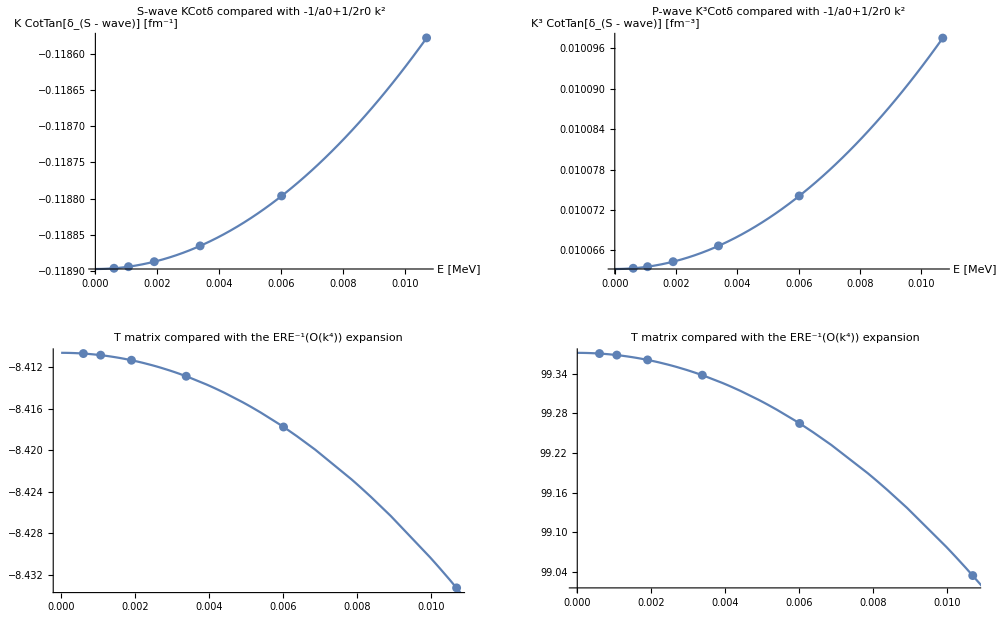

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 8.4106     r0 = 5.59155     a1 = -99.3714     r1 = 0.598634

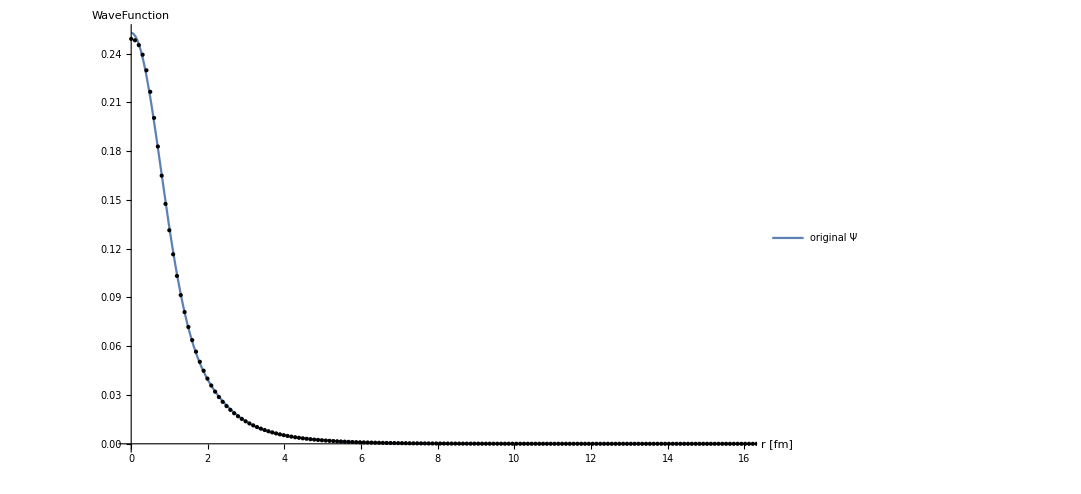

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{-0.58075,0.115341},{0.19373,1.10123},{0.351872,0.185055},{0.70137,0.115242},{-0.387053,0.154567}}

S Pole Poitions in momentum: {-0.173053+0.185929 ⅈ,0.+0.229434 ⅈ,0.-0.601292 ⅈ,0.173053+0.185929 ⅈ}

S Pole Poitions in energy:   {-0.127793-1.77914 ⅈ,-1.45535+0. ⅈ,-9.99595+0. ⅈ,-0.127793+1.77914 ⅈ}

P Pole Poitions in momentum: {-0.244702-0.307362 ⅈ,0.+0.14497 ⅈ,0.-0.343014 ⅈ,0.244702-0.307362 ⅈ}

P Pole Poitions in energy:   {-0.956388+4.15884 ⅈ,-0.581045+0. ⅈ,-3.25294+0. ⅈ,-0.956388-4.15884 ⅈ}

-0.118215+2.81198 p^2+13.2817 p^4

0.00944348+0.278513 p^2-1.23036 p^4

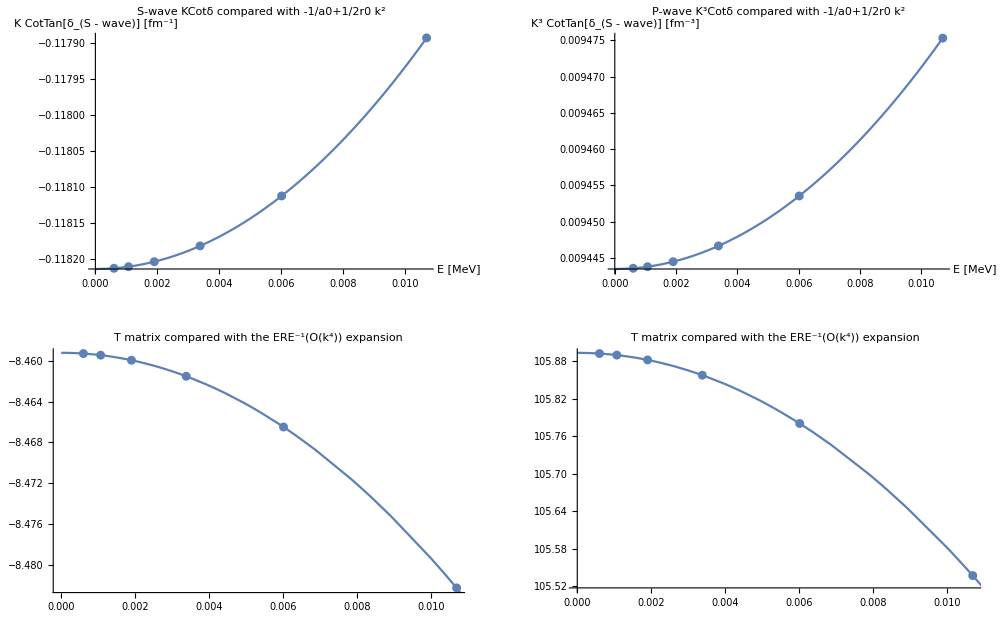

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 8.4592     r0 = 5.62428     a1 = -105.893     r1 = 0.556996

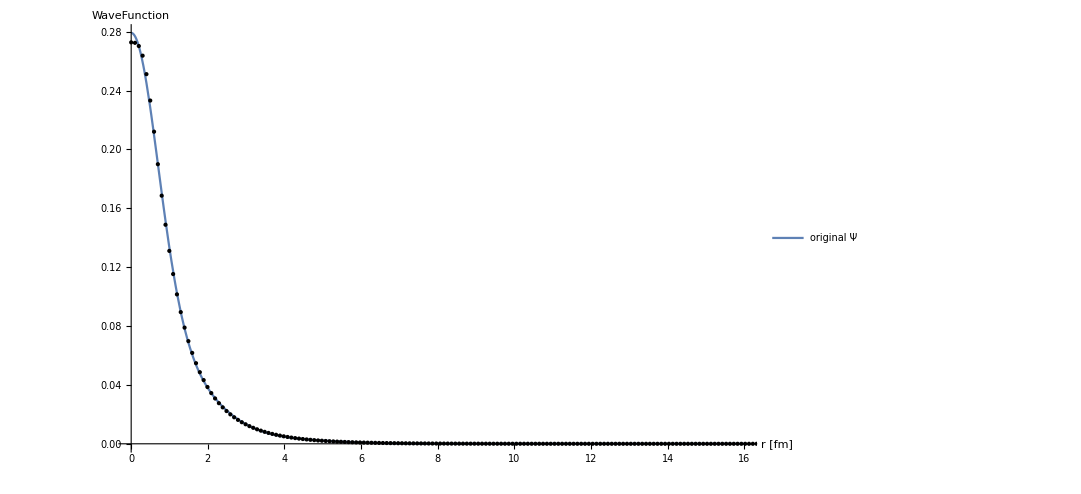

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-0.34271,0.10463},{0.238405,1.60983},{0.375862,0.104665},{0.374225,0.257065},{-0.299134,0.228594}}

S Pole Poitions in momentum: {-0.175293+0.187938 ⅈ,0.+0.232344 ⅈ,0.-0.608219 ⅈ,0.175293+0.187938 ⅈ}

S Pole Poitions in energy:   {-0.126977-1.82164 ⅈ,-1.49251+0. ⅈ,-10.2276+0. ⅈ,-0.126977+1.82164 ⅈ}

P Pole Poitions in momentum: {-0.208714-0.36079 ⅈ,0.+0.151665 ⅈ,0.-0.409826 ⅈ,0.208714-0.36079 ⅈ}

P Pole Poitions in energy:   {-2.39448+4.16381 ⅈ,-0.63595+0. ⅈ,-4.64357+0. ⅈ,-2.39448-4.16381 ⅈ}

-0.11975+2.77831 p^2+12.8299 p^4

0.0110218+0.304018 p^2-1.02068 p^4

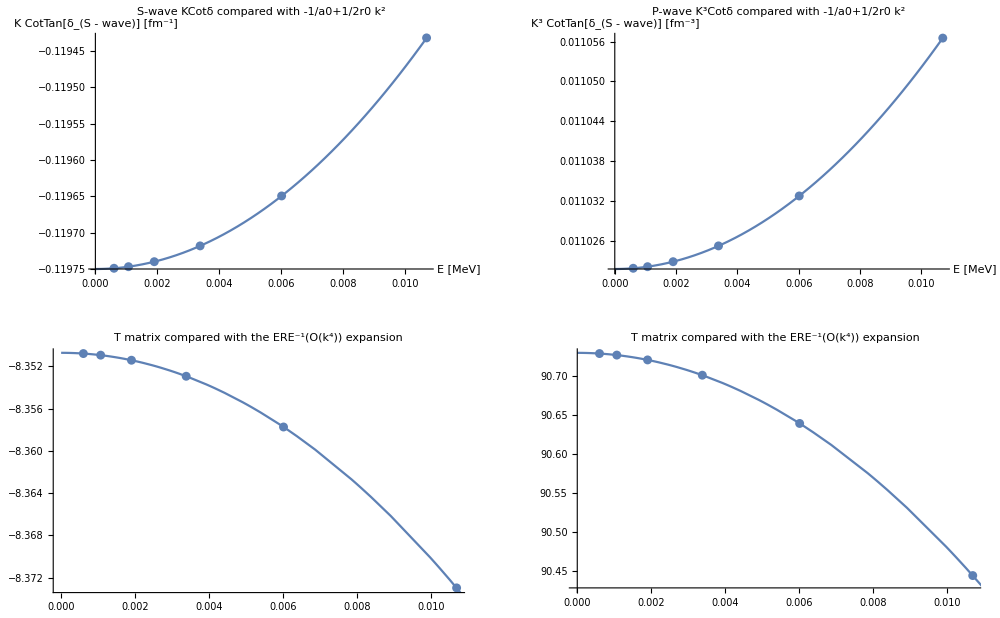

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 8.35073     r0 = 5.55693     a1 = -90.7297     r1 = 0.608011

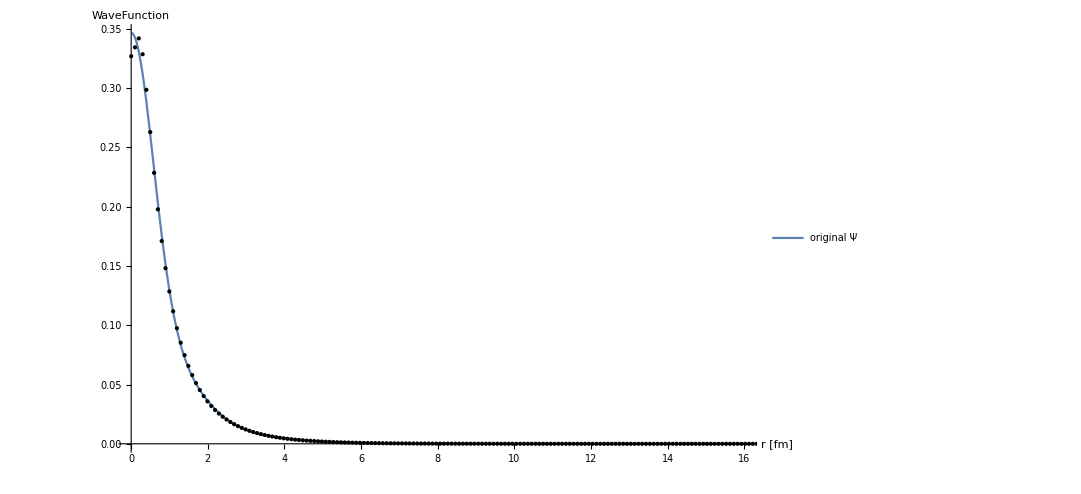

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{0.0391167,0.106371},{0.127497,0.467567},{-0.0431848,4.50467},{-0.0081534,0.0971119},{0.134202,1.75686}}

S Pole Poitions in momentum: {-0.278057+0.380842 ⅈ,0.+0.414431 ⅈ,0.-1.17612 ⅈ,0.278057+0.380842 ⅈ}

S Pole Poitions in energy:   {-1.87242-5.85547 ⅈ,-4.74852+0. ⅈ,-38.2431+0. ⅈ,-1.87242+5.85547 ⅈ}

P Pole Poitions in momentum: {-0.143997-0.401238 ⅈ,0.+0.322167 ⅈ,0.+0.762284 ⅈ,0.143997-0.401238 ⅈ}

P Pole Poitions in energy:   {-3.87773+3.19476 ⅈ,-2.86955+0. ⅈ,-16.0652+0. ⅈ,-3.87773-3.19476 ⅈ}

-0.200473+1.56342 p^2+1.84971 p^4

0.158273+1.57084 p^2+3.54642 p^4

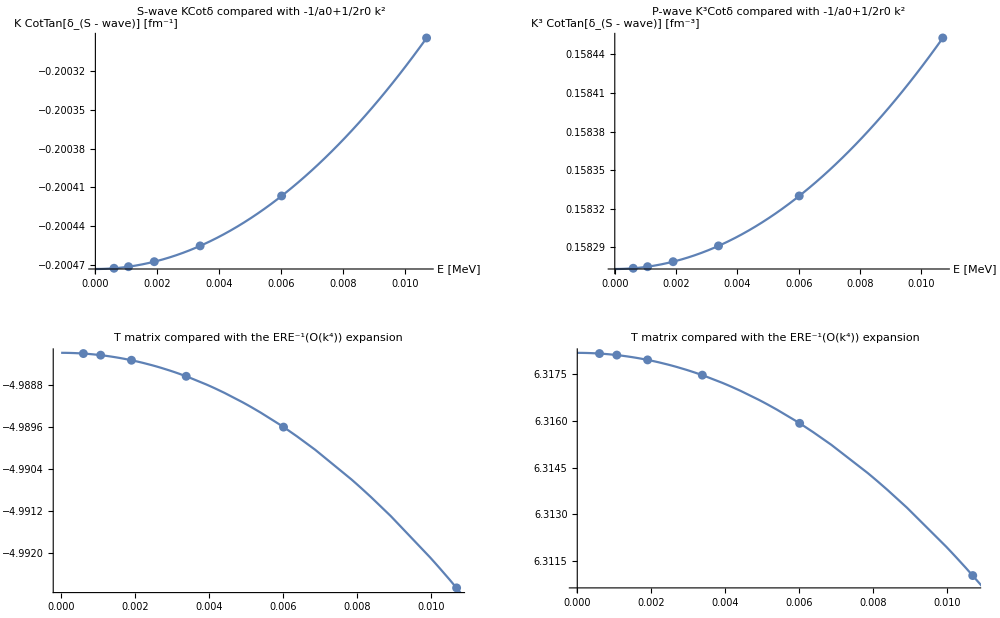

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 4.9882     r0 = 3.12689     a1 = -6.3182     r1 = 3.14176

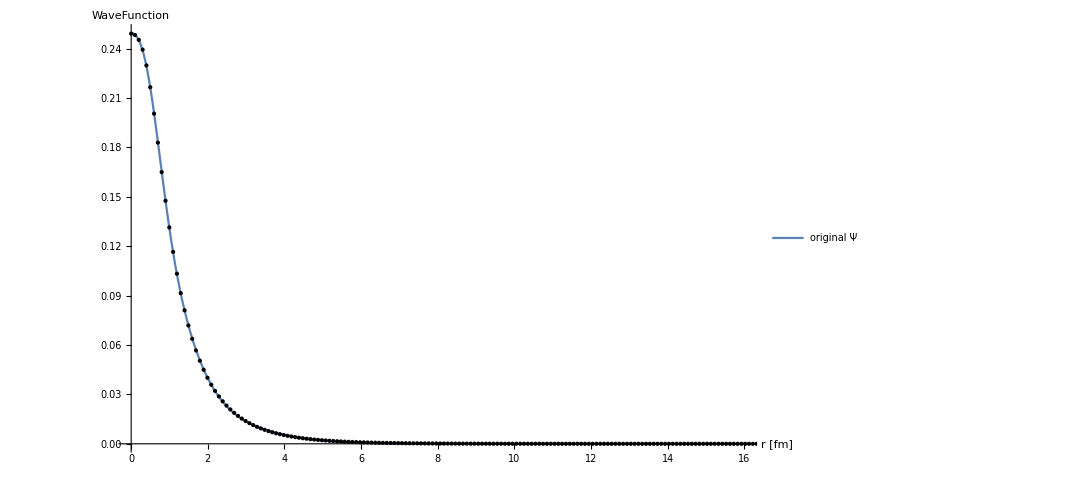

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{0.0797243,0.19999},{0.193233,1.10278},{0.0444201,0.0986326},{0.132768,0.201091},{-0.170973,0.161387}}

S Pole Poitions in momentum: {-4.39281-0.544969 ⅈ,-0.199717+0.544969 ⅈ,0.199717+0.544969 ⅈ,4.39281-0.544969 ⅈ}

S Pole Poitions in energy:   {525.293+132.372 ⅈ,-7.10825-6.01825 ⅈ,-7.10825+6.01825 ⅈ,525.293-132.372 ⅈ}

P Pole Poitions in momentum: {-0.248738-0.426713 ⅈ,-0.211693+0.477942 ⅈ,0.211693+0.477942 ⅈ,0.248738-0.426713 ⅈ}

P Pole Poitions in energy:   {-3.32359+5.86897 ⅈ,-5.07647-5.59456 ⅈ,-5.07647+5.59456 ⅈ,-3.32359-5.86897 ⅈ}

-0.314487+0.892984 p^2-0.0476445 p^4

0.650596+2.91416 p^2+9.76007 p^4

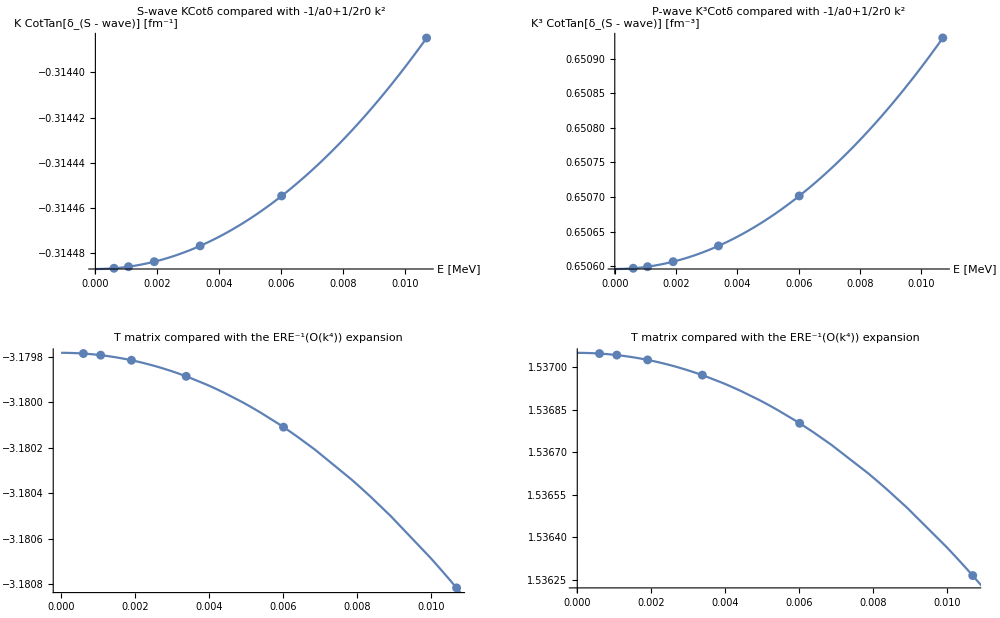

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 3.17978     r0 = 1.78597     a1 = -1.53705     r1 = 5.82856

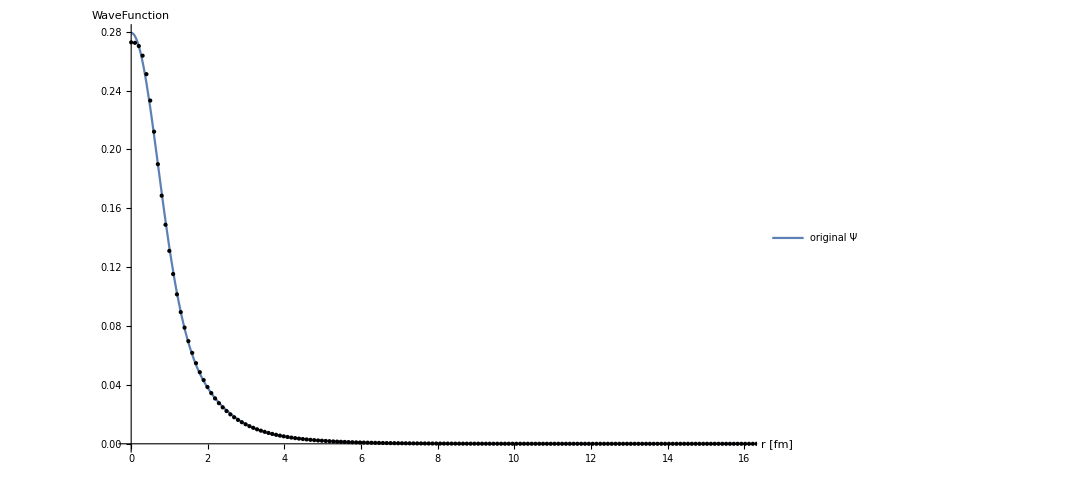

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-0.404892,0.232437},{0.480149,0.253985},{0.238403,1.60986},{0.278935,0.105163},{-0.245949,0.10519}}

S Pole Poitions in momentum: {-0.302227+0.335556 ⅈ,0.+0.405853 ⅈ,0.-1.07697 ⅈ,0.302227+0.335556 ⅈ}

S Pole Poitions in energy:   {-0.587692-5.60767 ⅈ,-4.55398+0. ⅈ,-32.0669+0. ⅈ,-0.587692+5.60767 ⅈ}

P Pole Poitions in momentum: {-0.216661-0.503043 ⅈ,0.+0.320281 ⅈ,0.+4.32101 ⅈ,0.216661-0.503043 ⅈ}

P Pole Poitions in energy:   {-5.69839+6.02655 ⅈ,-2.83606+0. ⅈ,-516.207+0. ⅈ,-5.69839-6.02655 ⅈ}

-0.207204+1.58888 p^2+2.32448 p^4

0.114209+0.821303 p^2+0.275088 p^4

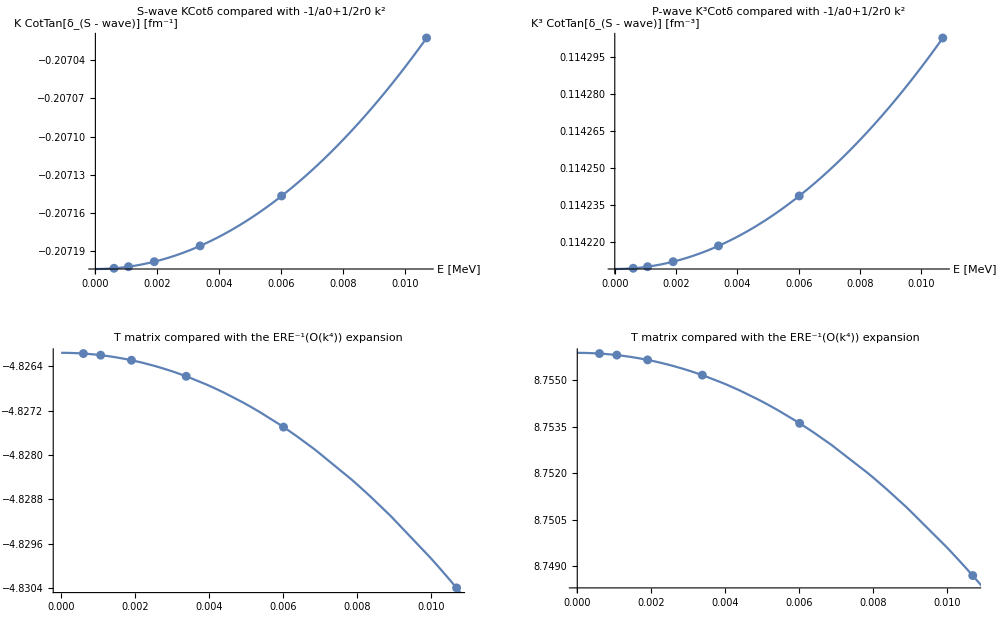

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 4.82616     r0 = 3.17783     a1 = -8.75589     r1 = 1.64261

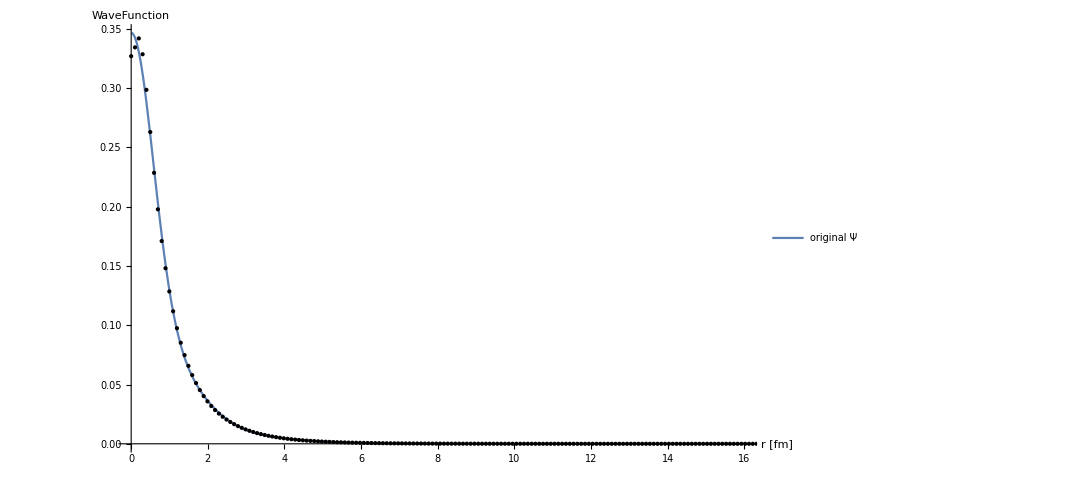

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{0.0703553,0.0836498},{-2.86095,0.56576},{-0.0520343,0.0836153},{1.73811,0.656655},{1.35726,0.481012}}

S Pole Poitions in momentum: {-0.197299+0.222911 ⅈ,0.+0.295655 ⅈ,0.-0.741476 ⅈ,0.197299+0.222911 ⅈ}

S Pole Poitions in energy:   {-0.297546-2.43187 ⅈ,-2.4167+0. ⅈ,-15.2001+0. ⅈ,-0.297546+2.43187 ⅈ}

P Pole Poitions in momentum: {-0.125723-0.32655 ⅈ,0.+0.193695 ⅈ,0.+5.84011 ⅈ,0.125723-0.32655 ⅈ}

P Pole Poitions in energy:   {-2.51117+2.27012 ⅈ,-1.03727+0. ⅈ,-942.966+0. ⅈ,-2.51117-2.27012 ⅈ}

-0.141551+2.39989 p^2+7.28649 p^4

0.0257412+0.499384 p^2+0.185849 p^4

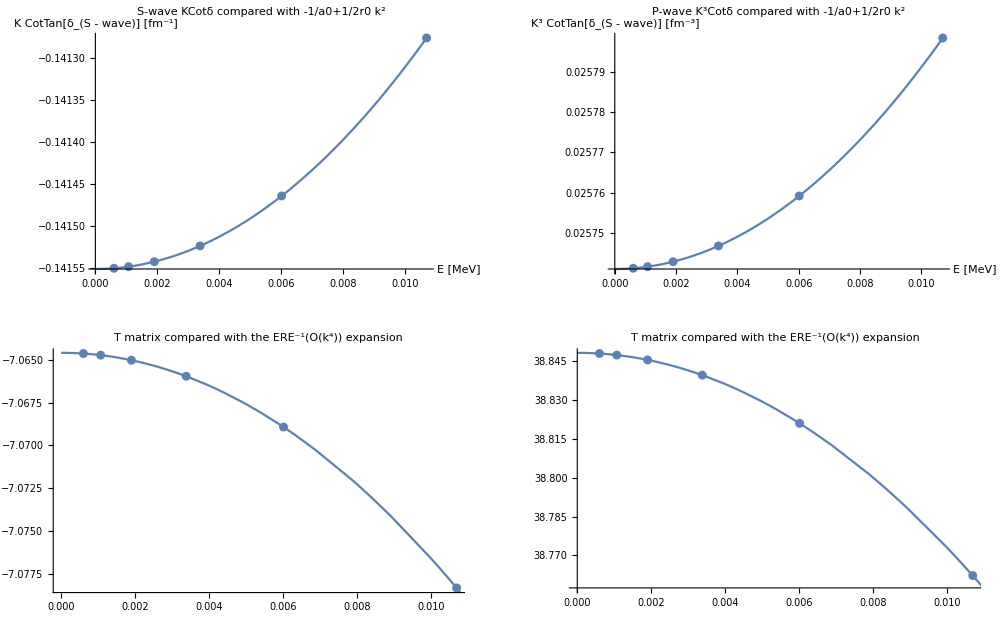

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 7.06459     r0 = 4.79996     a1 = -38.8482     r1 = 0.998773

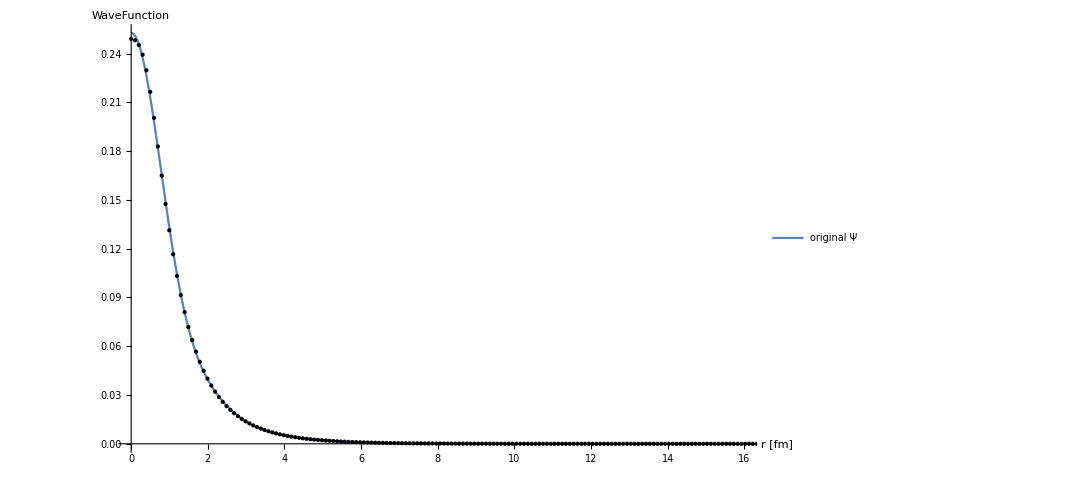

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{-0.0658685,0.057316},{-0.159598,0.0573168},{0.235585,0.0576407},{0.190851,1.10982},{0.0782171,0.258964}}

S Pole Poitions in momentum: {-0.167741+0.189853 ⅈ,0.+0.230962 ⅈ,0.-0.610667 ⅈ,0.167741+0.189853 ⅈ}

S Pole Poitions in energy:   {-0.218604-1.76092 ⅈ,-1.4748+0. ⅈ,-10.3101+0. ⅈ,-0.218604+1.76092 ⅈ}

P Pole Poitions in momentum: {-0.126356-0.297874 ⅈ,0.+0.139583 ⅈ,0.-0.678487 ⅈ,0.126356-0.297874 ⅈ}

P Pole Poitions in energy:   {-2.01171+2.08119 ⅈ,-0.538665+0. ⅈ,-12.7273+0. ⅈ,-2.01171-2.08119 ⅈ}

-0.116167+2.83656 p^2+12.833 p^4

0.00873851+0.291756 p^2-0.881327 p^4

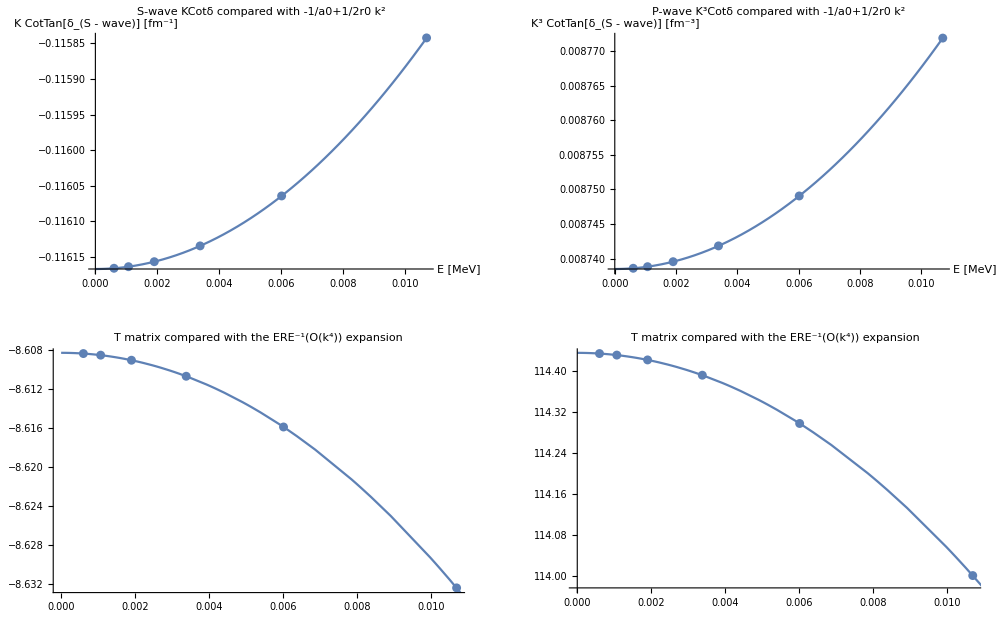

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 8.60831     r0 = 5.67344     a1 = -114.436     r1 = 0.583489

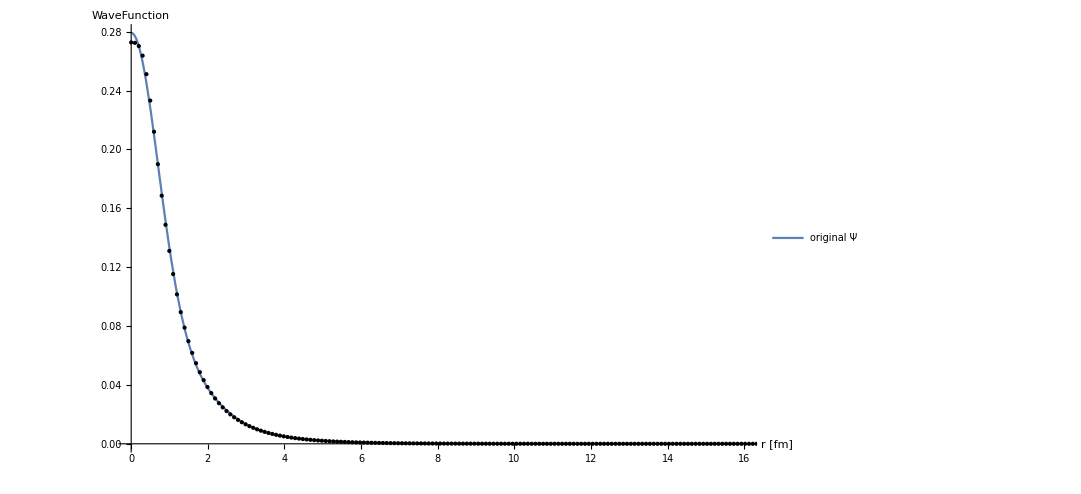

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{1.35462,1.13891},{0.0274017,0.10804},{0.559852,0.706122},{0.38916,0.703812},{-1.98462,0.910056}}

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

S Pole Poitions in momentum: {-1.49383-0.718739 ⅈ,-0.431478+0.718739 ⅈ,0.431478+0.718739 ⅈ,1.49383-0.718739 ⅈ}

S Pole Poitions in energy:   {47.4134+59.3684 ⅈ,-9.13504-17.148 ⅈ,-9.13504+17.148 ⅈ,47.4134-59.3684 ⅈ}

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

P Pole Poitions in momentum: {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

P Pole Poitions in energy:   {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

-0.656859+0.470903 p^2-0.340119 p^4

Fit[{{0.000601414,ComplexInfinity},{0.00106948,6.48024},{0.00190184,6.48022},{0.003382,6.48014},{0.00601414,6.4799},{0.0106948,6.47915}},{1,p^2,p^4},p]

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ListPlot::prng: Value of option PlotRange -> {{0.000601414,ComplexInfinity},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

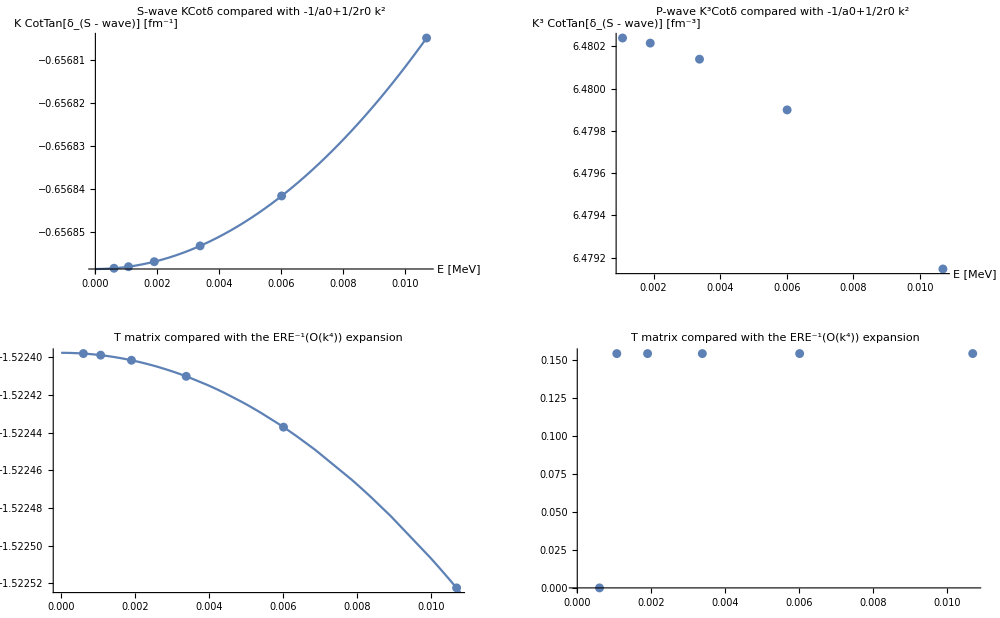

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 1.5224     r0 = 0.941798     a1 = -1/Fit[{{0.000601414,ComplexInfinity},{0.00106948,6.48024},{0.00190184,6.48022},{0.003382,6.48014}},{1,p^2},p]     r1 = 0.

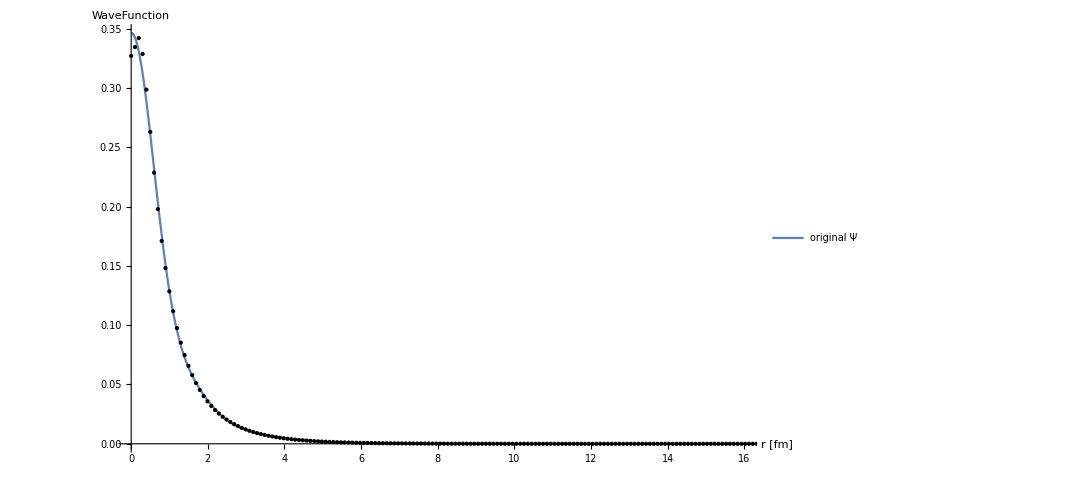

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{-0.640128,0.137476},{0.368046,0.161581},{0.0837369,0.161485},{0.265822,0.115448},{0.175399,0.931584}}

S Pole Poitions in momentum: {-0.188587+0.203481 ⅈ,0.+0.250292 ⅈ,0.-0.657255 ⅈ,0.188587+0.203481 ⅈ}

S Pole Poitions in energy:   {-0.161452-2.12187 ⅈ,-1.73199+0. ⅈ,-11.9432+0. ⅈ,-0.161452+2.12187 ⅈ}

P Pole Poitions in momentum: {-0.27128-0.362881 ⅈ,0.+0.16505 ⅈ,0.-0.396319 ⅈ,0.27128-0.362881 ⅈ}

P Pole Poitions in energy:   {-1.60603+5.44333 ⅈ,-0.753153+0. ⅈ,-4.34252+0. ⅈ,-1.60603-5.44333 ⅈ}

-0.128847+2.57608 p^2+10.1759 p^4

0.0140304+0.321525 p^2-1.0449 p^4

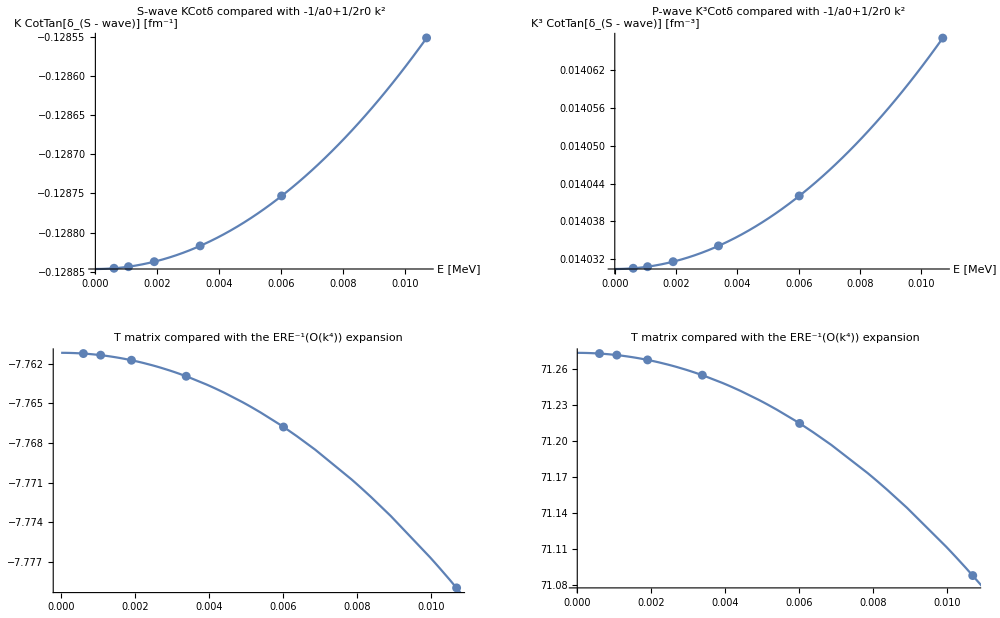

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 7.76117     r0 = 5.1524     a1 = -71.2739     r1 = 0.643023

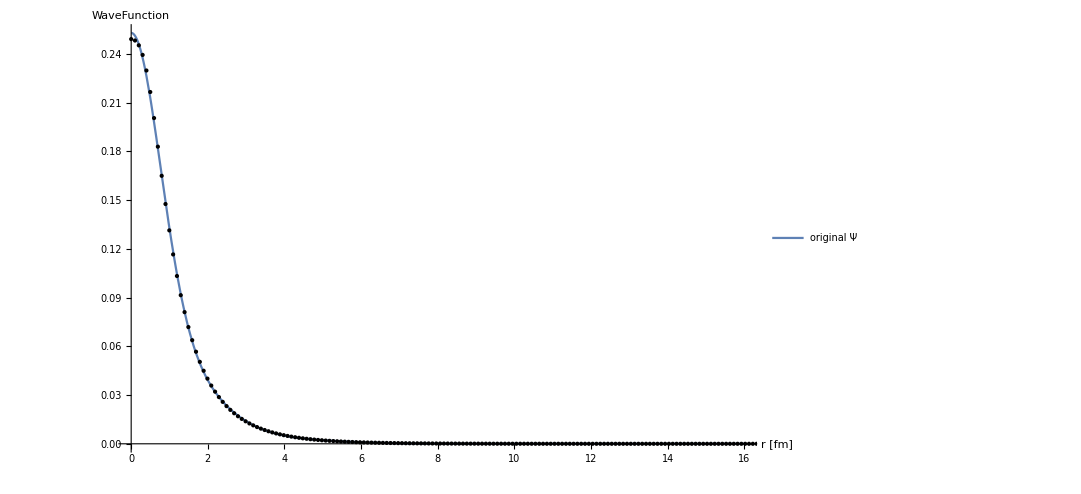

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{-0.268663,1.03006},{-0.224513,0.17862},{-0.292531,1.03005},{0.29449,0.178619},{0.76991,1.03012}}

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

S Pole Poitions in momentum: {-0.44734-0.504355 ⅈ,-0.389219+0.504355 ⅈ,0.389219+0.504355 ⅈ,0.44734-0.504355 ⅈ}

S Pole Poitions in energy:   {-1.50017+12.4755 ⅈ,-2.84443-10.8546 ⅈ,-2.84443+10.8546 ⅈ,-1.50017-12.4755 ⅈ}

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

P Pole Poitions in momentum: {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

P Pole Poitions in energy:   {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

-3.76102-3.20405 p^2-20.3893 p^4

Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,63.6426},{0.003382,63.6312},{0.00601414,63.5953},{0.0106948,63.4826}},{1,p^2,p^4},p]

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ListPlot::prng: Value of option PlotRange -> {{0.000601414,ComplexInfinity},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

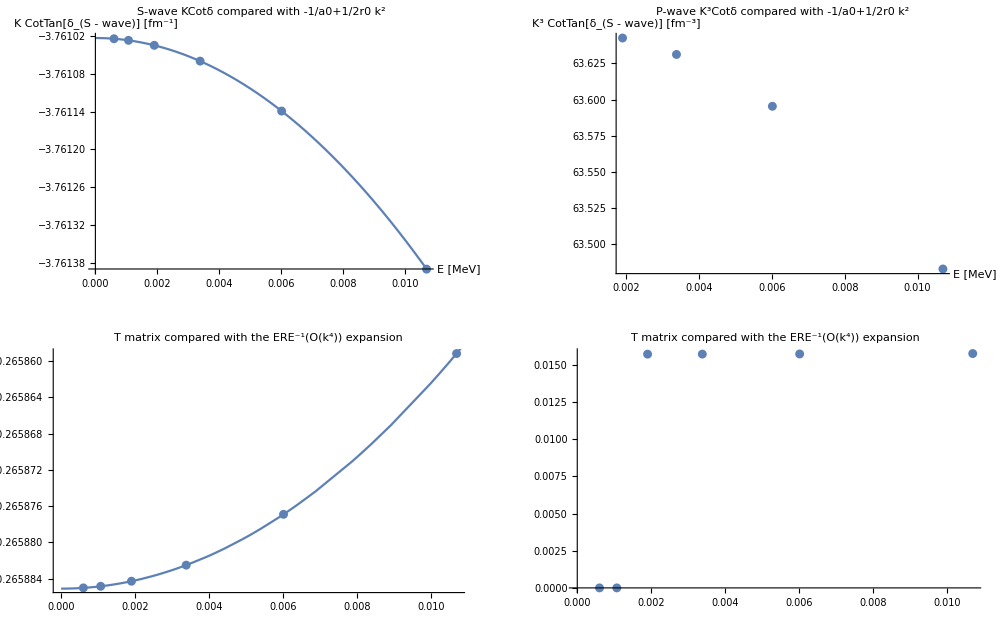

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 0.265885     r0 = -6.4086     a1 = -1/Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,63.6426},{0.003382,63.6312}},{1,p^2},p]     r1 = 0.

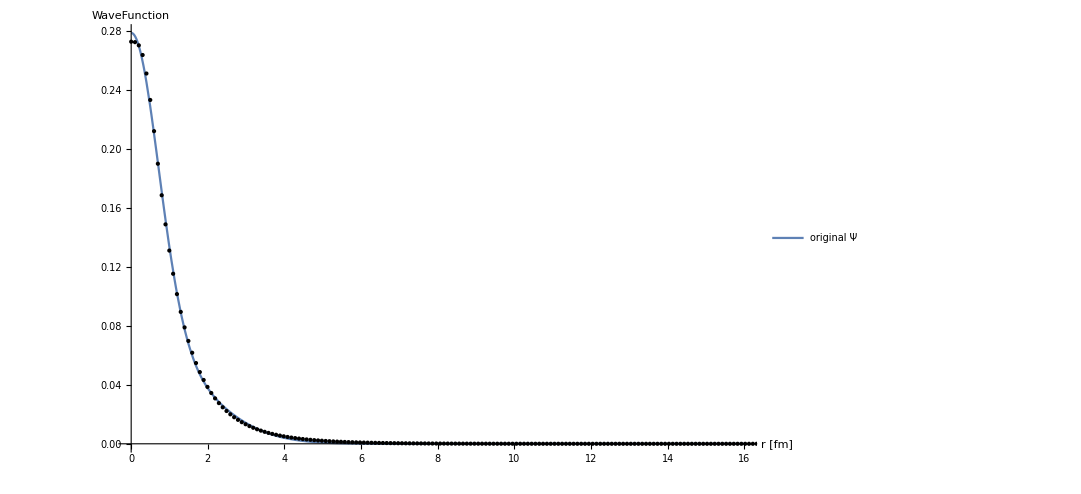

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-0.290482,0.14025},{0.239186,1.60653},{0.4547,0.139242},{0.22345,0.253921},{-0.280216,0.173585}}

S Pole Poitions in momentum: {-0.193159+0.288725 ⅈ,0.+0.354542 ⅈ,0.-0.931993 ⅈ,0.193159+0.288725 ⅈ}

S Pole Poitions in energy:   {-1.27321-3.08378 ⅈ,-3.47528+0. ⅈ,-24.0148+0. ⅈ,-1.27321+3.08378 ⅈ}

P Pole Poitions in momentum: {-0.157034-0.407177 ⅈ,0.+0.212757 ⅈ,0.-2.3567 ⅈ,0.157034-0.407177 ⅈ}

P Pole Poitions in energy:   {-3.90196+3.53558 ⅈ,-1.25147+0. ⅈ,-153.554+0. ⅈ,-3.90196-3.53558 ⅈ}

-0.153073+2.08533 p^2+3.83892 p^4

0.0322799+0.485069 p^2-0.338033 p^4

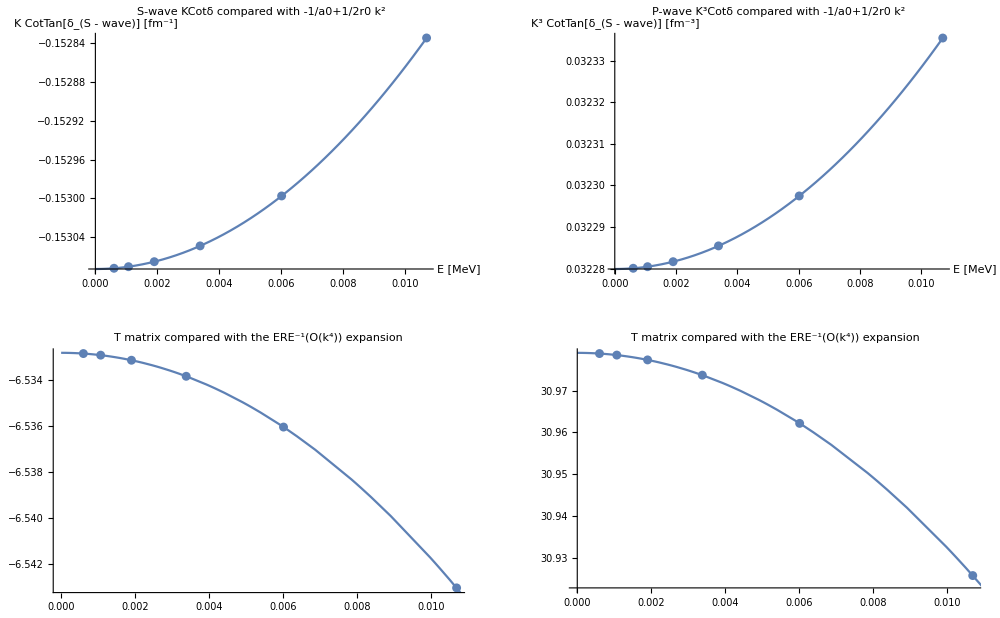

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 6.53283     r0 = 4.17075     a1 = -30.979     r1 = 0.970129

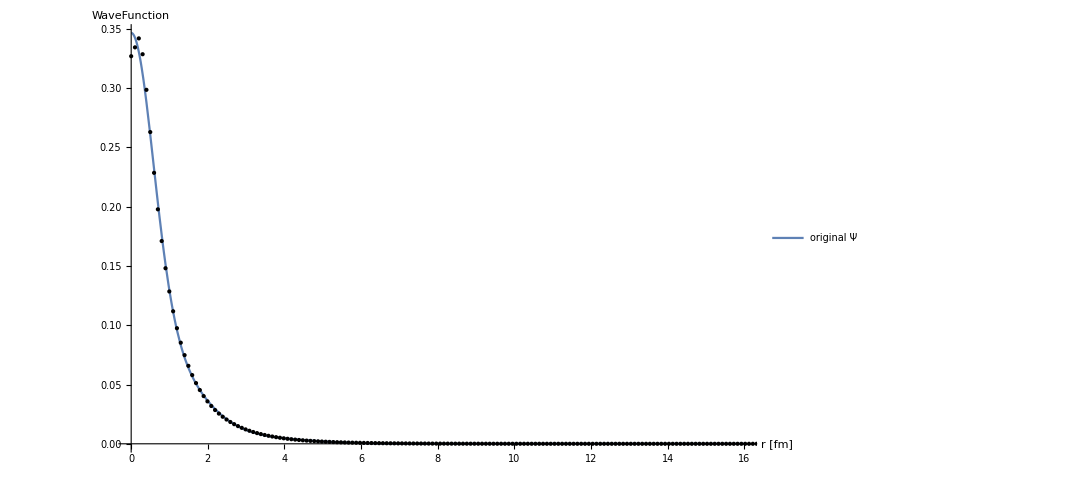

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{0.308327,0.102744},{0.175175,0.93222},{-0.228353,0.10275},{0.550778,0.164634},{-0.55305,0.150255}}

S Pole Poitions in momentum: {-0.176131+0.189112 ⅈ,0.+0.233567 ⅈ,0.-0.61179 ⅈ,0.176131+0.189112 ⅈ}

S Pole Poitions in energy:   {-0.131073-1.84178 ⅈ,-1.50827+0. ⅈ,-10.3481+0. ⅈ,-0.131073+1.84178 ⅈ}

P Pole Poitions in momentum: {-0.224701-0.355706 ⅈ,0.+0.151901 ⅈ,0.-0.389964 ⅈ,0.224701-0.355706 ⅈ}

P Pole Poitions in energy:   {-2.1022+4.41956 ⅈ,-0.637934+0. ⅈ,-4.20438+0. ⅈ,-2.1022-4.41956 ⅈ}

-0.120335+2.7635 p^2+12.6094 p^4

0.0110438+0.302422 p^2-1.05321 p^4

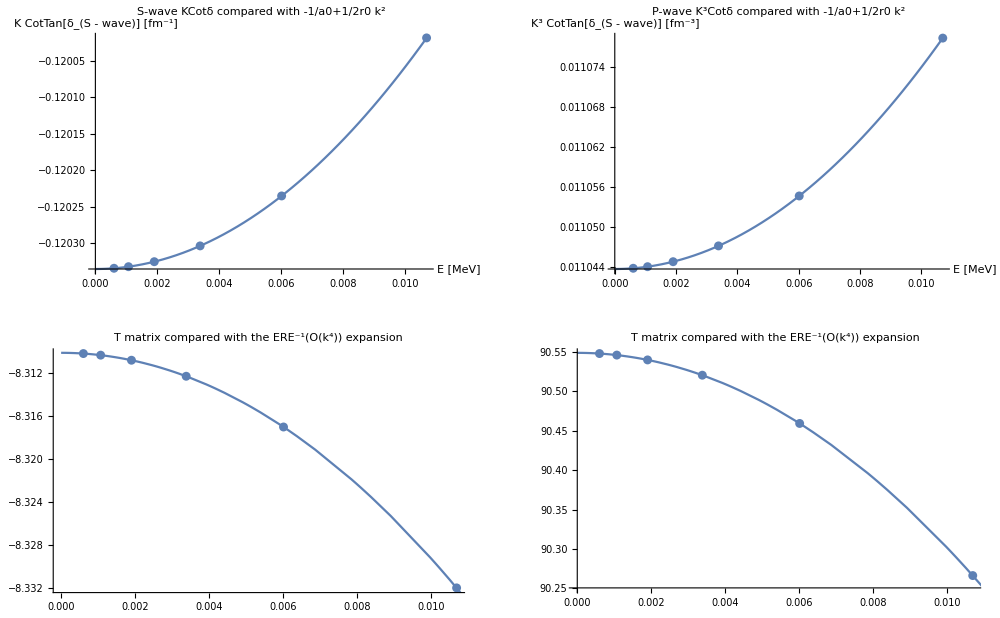

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 8.31013     r0 = 5.52731     a1 = -90.5489     r1 = 0.604817

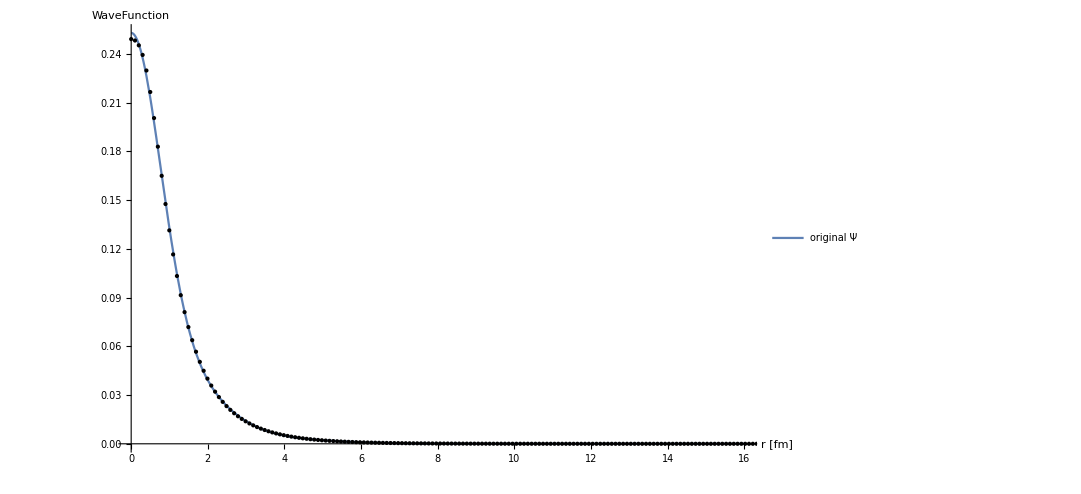

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{0.301473,0.124887},{-0.156177,0.150435},{0.193905,1.10067},{0.413217,0.179791},{-0.47325,0.14669}}

S Pole Poitions in momentum: {-0.199452+0.216326 ⅈ,0.+0.265104 ⅈ,0.-0.697757 ⅈ,0.199452+0.216326 ⅈ}

S Pole Poitions in energy:   {-0.193967-2.38579 ⅈ,-1.94306+0. ⅈ,-13.4605+0. ⅈ,-0.193967+2.38579 ⅈ}

P Pole Poitions in momentum: {-0.163805-0.419509 ⅈ,0.+0.184688 ⅈ,0.-0.78262 ⅈ,0.163805-0.419509 ⅈ}

P Pole Poitions in energy:   {-4.12375+3.79973 ⅈ,-0.943046+0. ⅈ,-16.9338+0. ⅈ,-4.12375-3.79973 ⅈ}

-0.136311+2.43075 p^2+8.51139 p^4

0.0204014+0.389682 p^2-0.695919 p^4

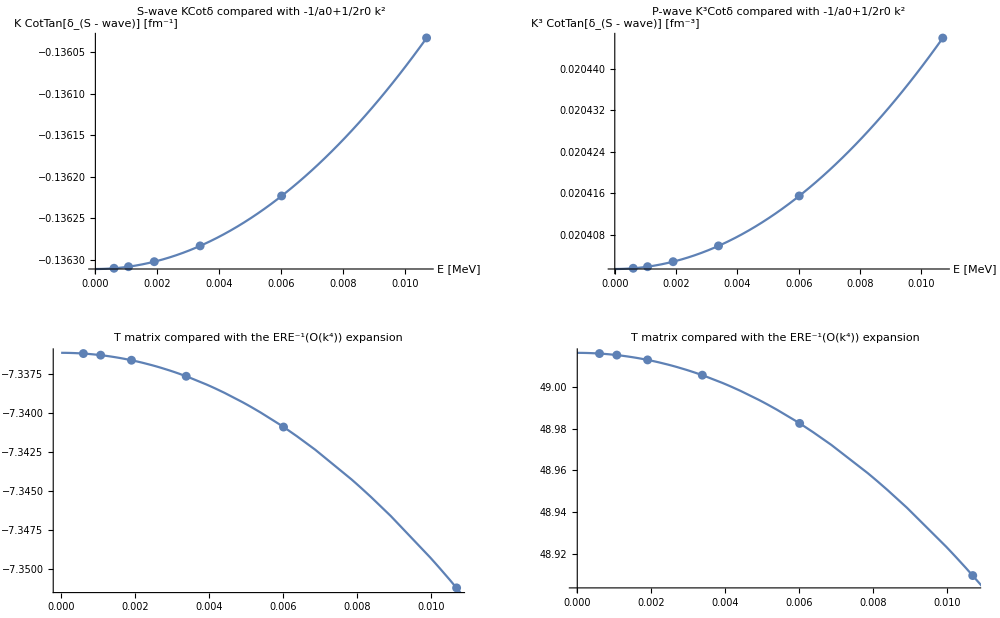

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 7.33618     r0 = 4.86171     a1 = -49.0163     r1 = 0.779348

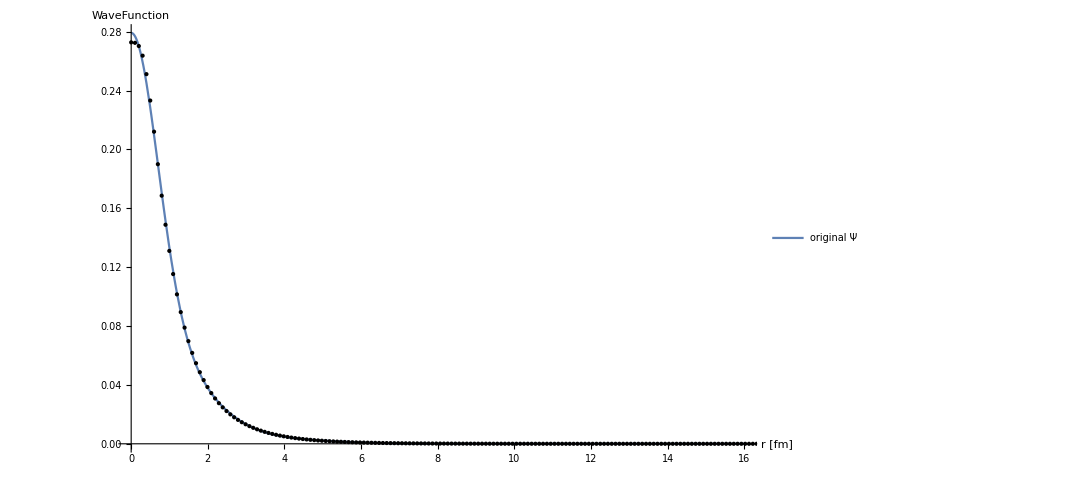

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-19.6782,0.843875},{-5.11817,0.653534},{15.105,0.725648},{10.0028,0.939024},{0.0348957,0.12183}}

S Pole Poitions in momentum: {-0.4181+0.463344 ⅈ,0.+0.573945 ⅈ,0.-1.50063 ⅈ,0.4181+0.463344 ⅈ}

S Pole Poitions in energy:   {-1.10259-10.7119 ⅈ,-9.1074+0. ⅈ,-62.2591+0. ⅈ,-1.10259+10.7119 ⅈ}

P Pole Poitions in momentum: {-0.367654-0.589281 ⅈ,0.+0.361783 ⅈ,0.-3.11455 ⅈ,0.367654-0.589281 ⅈ}

P Pole Poitions in energy:   {-5.86352+11.9797 ⅈ,-3.61868+0. ⅈ,-268.19+0. ⅈ,-5.86352-11.9797 ⅈ}

-0.289424+1.14793 p^2+0.862753 p^4

0.138271+0.661338 p^2-0.254367 p^4

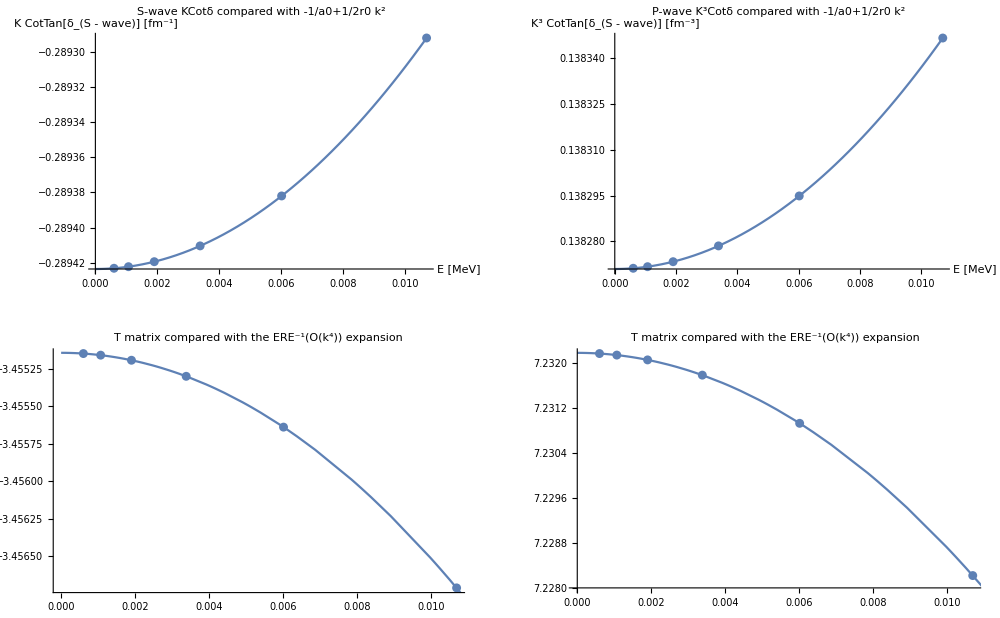

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 3.45514     r0 = 2.29587     a1 = -7.23218     r1 = 1.32267

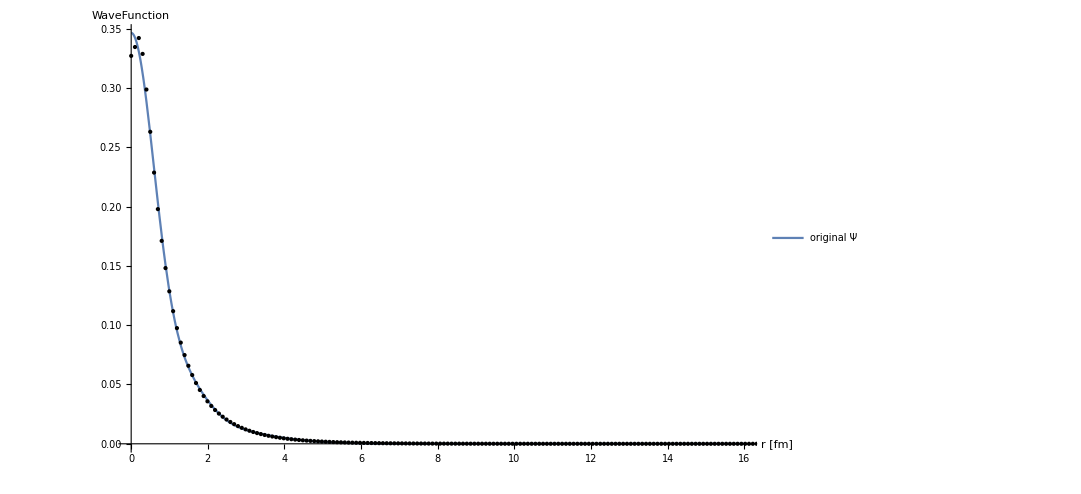

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{-0.206226,0.813435},{0.395346,0.841508},{0.351886,0.162997},{-0.17747,0.162972},{-0.111101,0.163067}}

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

S Pole Poitions in momentum: {-0.457211-0.536727 ⅈ,-0.376694+0.536727 ⅈ,0.376694+0.536727 ⅈ,0.457211-0.536727 ⅈ}

S Pole Poitions in energy:   {-2.18507+13.5692 ⅈ,-4.04143-11.1796 ⅈ,-4.04143+11.1796 ⅈ,-2.18507-13.5692 ⅈ}

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

P Pole Poitions in momentum: {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

P Pole Poitions in energy:   {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

-2.96558-3.12463 p^2-13.8742 p^4

Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,34.4804},{0.003382,34.4772},{0.00601414,34.4671},{0.0106948,34.4354}},{1,p^2,p^4},p]

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ListPlot::prng: Value of option PlotRange -> {{0.000601414,ComplexInfinity},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

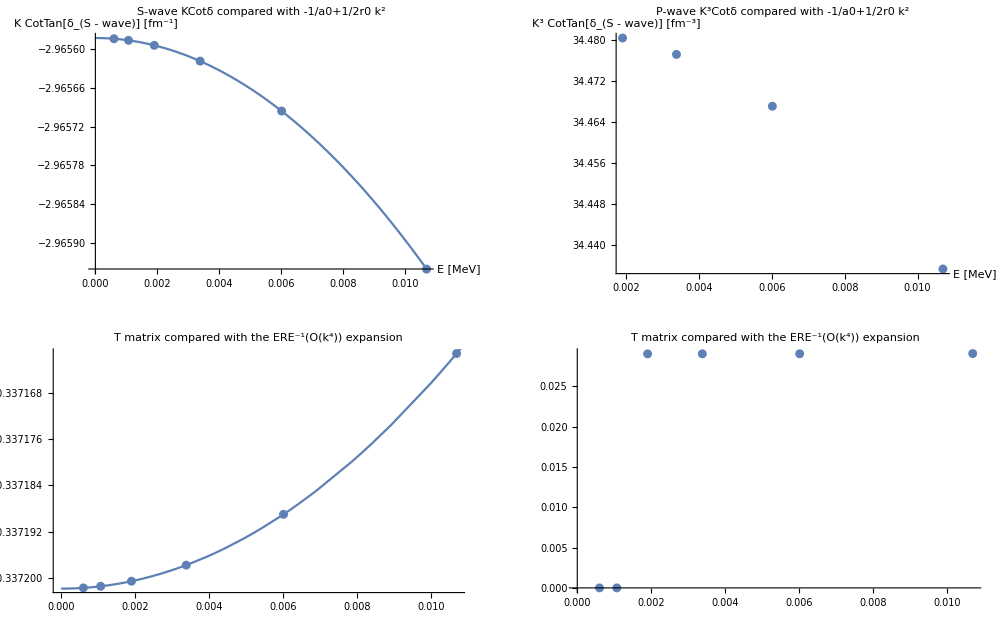

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 0.337202     r0 = -6.2496     a1 = -1/Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,34.4804},{0.003382,34.4772}},{1,p^2},p]     r1 = 0.

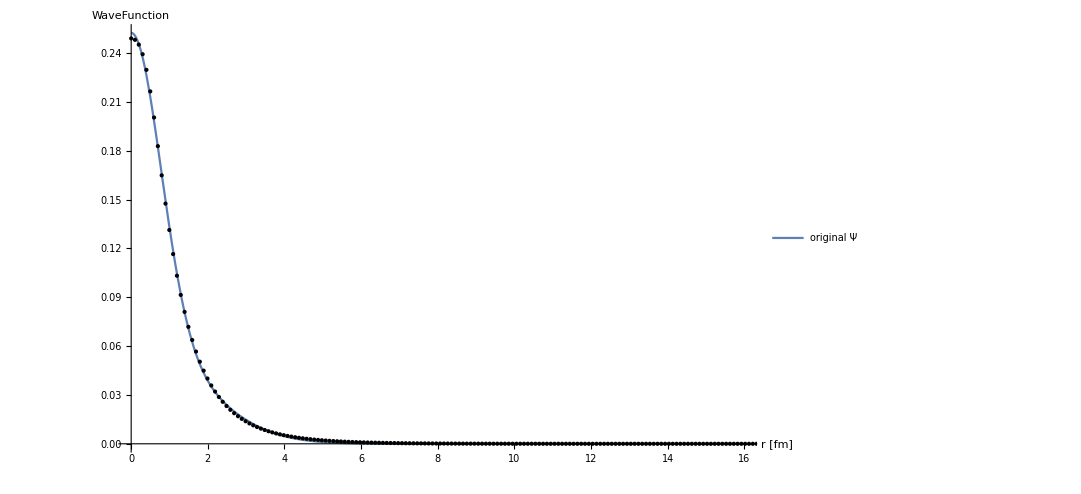

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{-2.78153,0.654807},{-0.531722,0.0888055},{1.29017,0.545002},{0.552453,0.0888606},{1.74963,0.769261}}

S Pole Poitions in momentum: {-0.458244+0.539052 ⅈ,0.+0.662154 ⅈ,0.-1.74026 ⅈ,0.458244+0.539052 ⅈ}

S Pole Poitions in energy:   {-2.2281-13.6587 ⅈ,-12.1219+0. ⅈ,-83.7299+0. ⅈ,-2.2281+13.6587 ⅈ}

P Pole Poitions in momentum: {-0.350962-0.502977 ⅈ,0.+0.513098 ⅈ,0.+1.37869 ⅈ,0.350962-0.502977 ⅈ}

P Pole Poitions in energy:   {-3.58895+9.76094 ⅈ,-7.2787+0. ⅈ,-52.5519+0. ⅈ,-3.58895-9.76094 ⅈ}

-0.32369+1.018 p^2+0.561173 p^4

0.300391+0.925103 p^2+1.12888 p^4

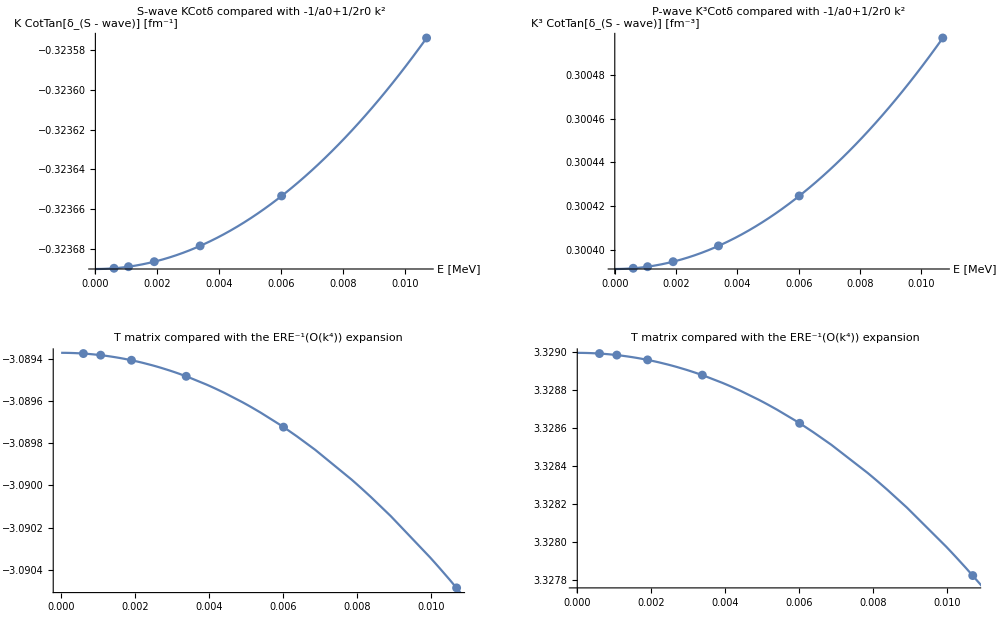

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 3.08937     r0 = 2.03602     a1 = -3.32899     r1 = 1.85023

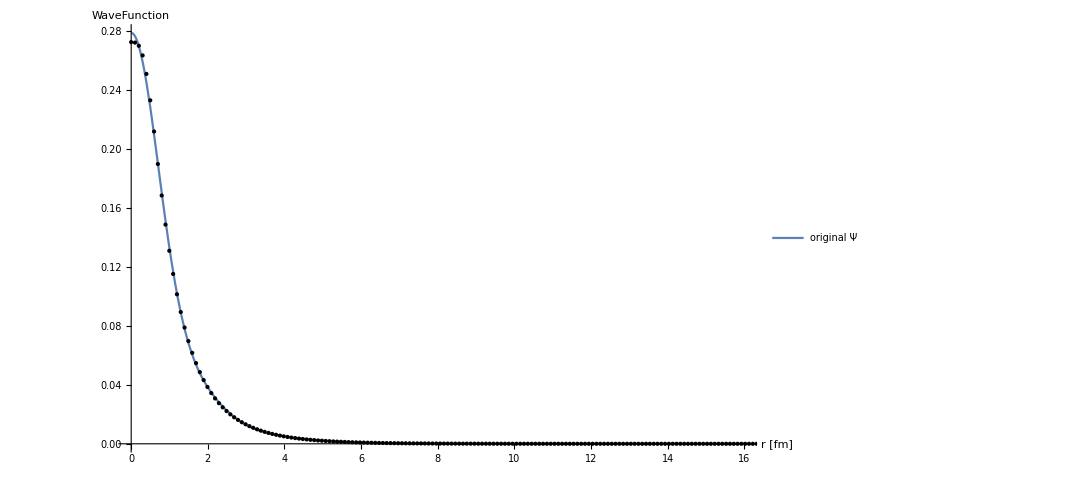

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{0.452313,0.105119},{0.531603,0.252528},{-0.418966,0.105108},{-0.456737,0.233125},{0.238434,1.60972}}

S Pole Poitions in momentum: {-0.170015+0.182459 ⅈ,0.+0.225421 ⅈ,0.-0.590339 ⅈ,0.170015+0.182459 ⅈ}

S Pole Poitions in energy:   {-0.121263-1.71529 ⅈ,-1.40489+0. ⅈ,-9.6351+0. ⅈ,-0.121263+1.71529 ⅈ}

P Pole Poitions in momentum: {-0.231648-0.311855 ⅈ,0.+0.142258 ⅈ,0.-0.345233 ⅈ,0.231648-0.311855 ⅈ}

P Pole Poitions in energy:   {-1.20522+3.99452 ⅈ,-0.559511+0. ⅈ,-3.29518+0. ⅈ,-1.20522-3.99452 ⅈ}

-0.116152+2.86345 p^2+14.0335 p^4

0.00896563+0.276284 p^2-1.20965 p^4

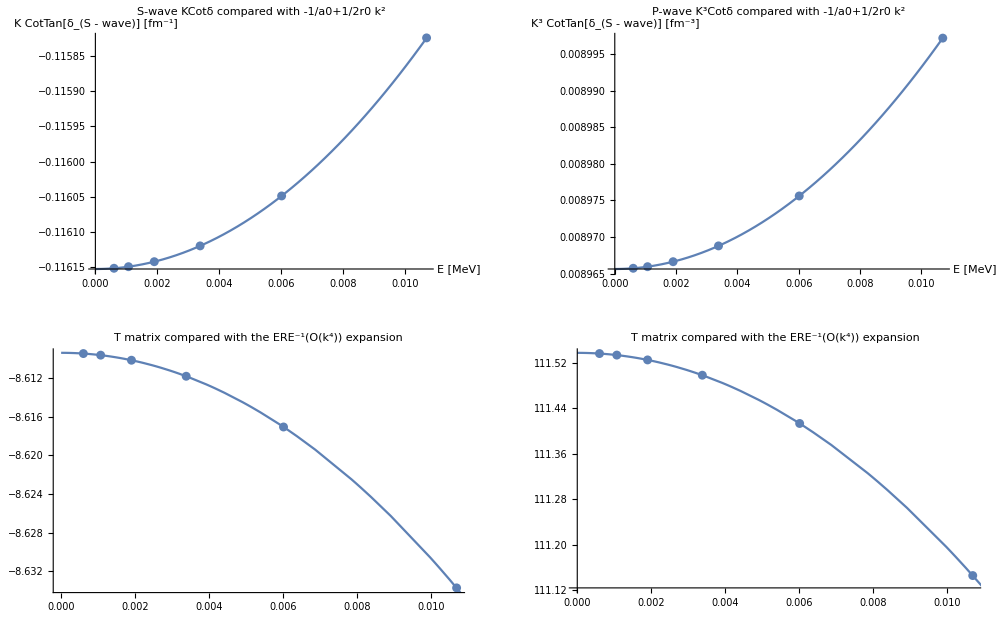

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 8.60938     r0 = 5.72724     a1 = -111.537     r1 = 0.552537

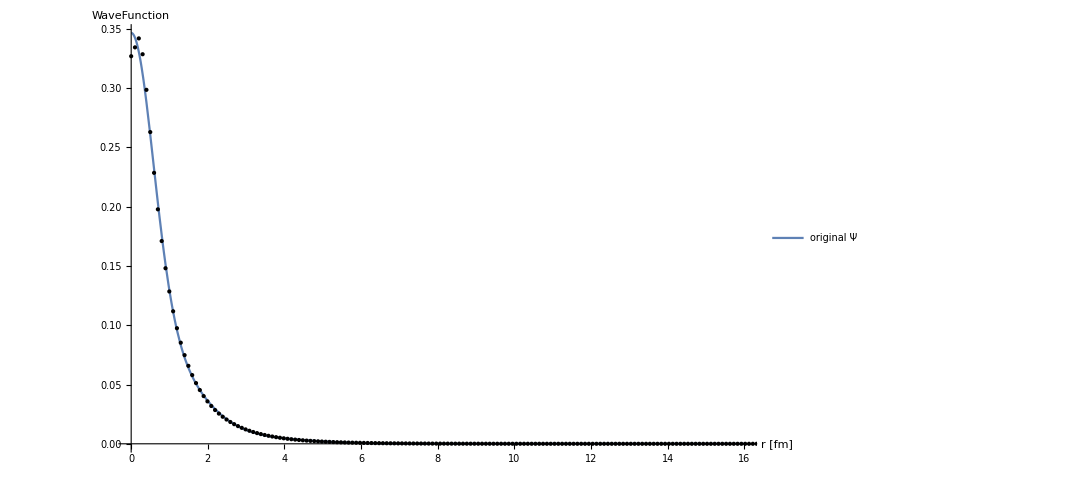

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{-0.159382,0.100902},{-0.603061,0.152004},{0.175147,0.932297},{0.232151,0.101074},{0.608023,0.164621}}

S Pole Poitions in momentum: {-0.194217+0.212754 ⅈ,0.+0.259163 ⅈ,0.-0.684671 ⅈ,0.194217+0.212754 ⅈ}

S Pole Poitions in energy:   {-0.208578-2.2848 ⅈ,-1.85695+0. ⅈ,-12.9604+0. ⅈ,-0.208578+2.2848 ⅈ}

P Pole Poitions in momentum: {-0.138694-0.364461 ⅈ,0.+0.17953 ⅈ,0.-1.28752 ⅈ,0.138694-0.364461 ⅈ}

P Pole Poitions in energy:   {-3.14063+2.79507 ⅈ,-0.891107+0. ⅈ,-45.8311+0. ⅈ,-3.14063-2.79507 ⅈ}

-0.13288+2.48629 p^2+9.02418 p^4

0.0191356+0.396621 p^2-0.544392 p^4

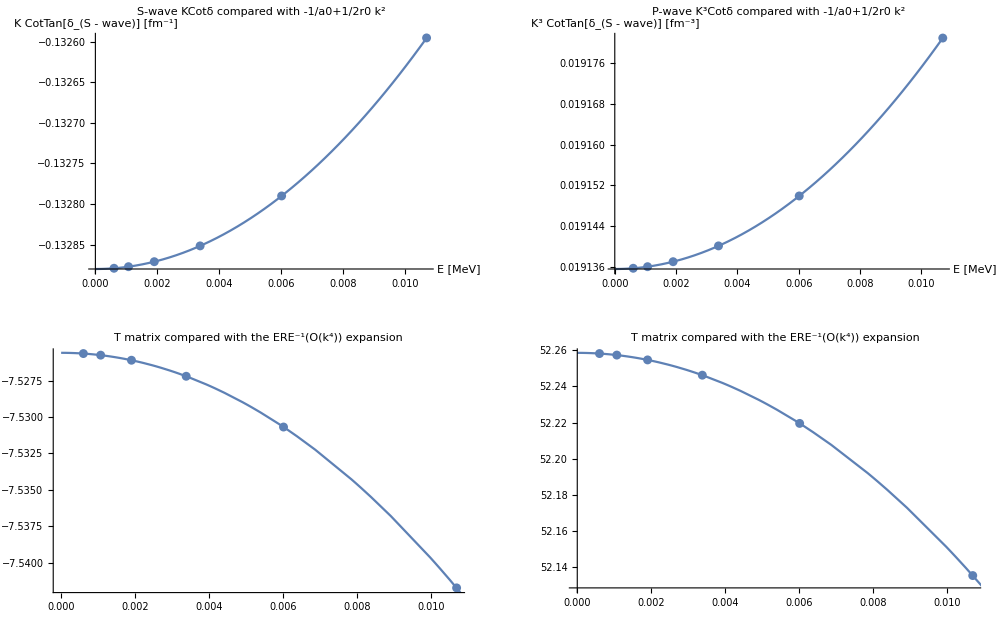

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 7.52559     r0 = 4.97281     a1 = -52.2587     r1 = 0.793228

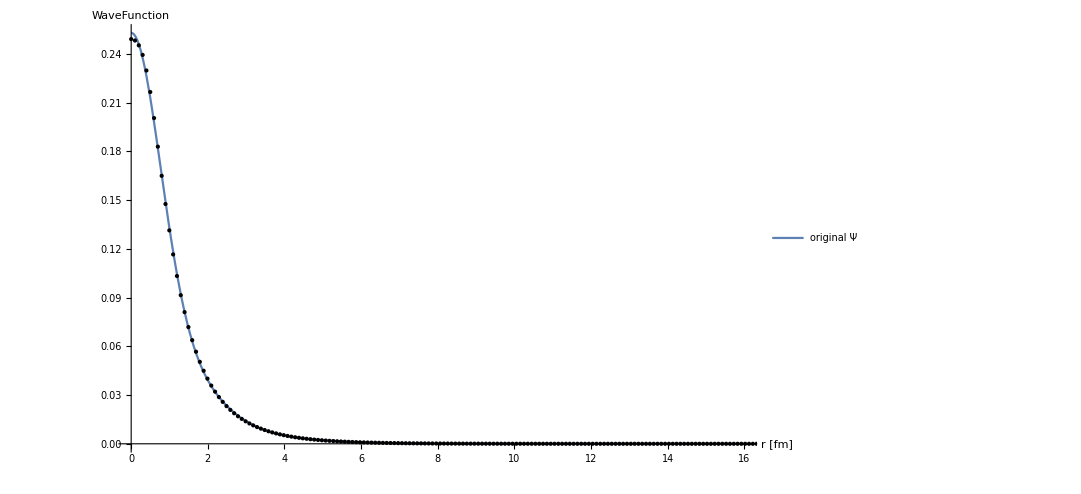

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{-0.344168,0.178618},{0.583332,1.03031},{-0.118825,0.178618},{-0.374617,1.03031},{0.532971,0.178618}}

S Pole Poitions in momentum: {-0.254233+0.284457 ⅈ,0.+0.34177 ⅈ,0.-0.910684 ⅈ,0.254233+0.284457 ⅈ}

S Pole Poitions in energy:   {-0.450135-3.99881 ⅈ,-3.2294+0. ⅈ,-22.9292+0. ⅈ,-0.450135+3.99881 ⅈ}

P Pole Poitions in momentum: {-0.187938-0.488704 ⅈ,0.+0.251641 ⅈ,0.-2.44665 ⅈ,0.187938-0.488704 ⅈ}

P Pole Poitions in energy:   {-5.62652+5.07861 ⅈ,-1.75071+0. ⅈ,-165.5+0. ⅈ,-5.62652-5.07861 ⅈ}

-0.17432+1.88304 p^2+3.84798 p^4

0.0532052+0.568618 p^2-0.315217 p^4

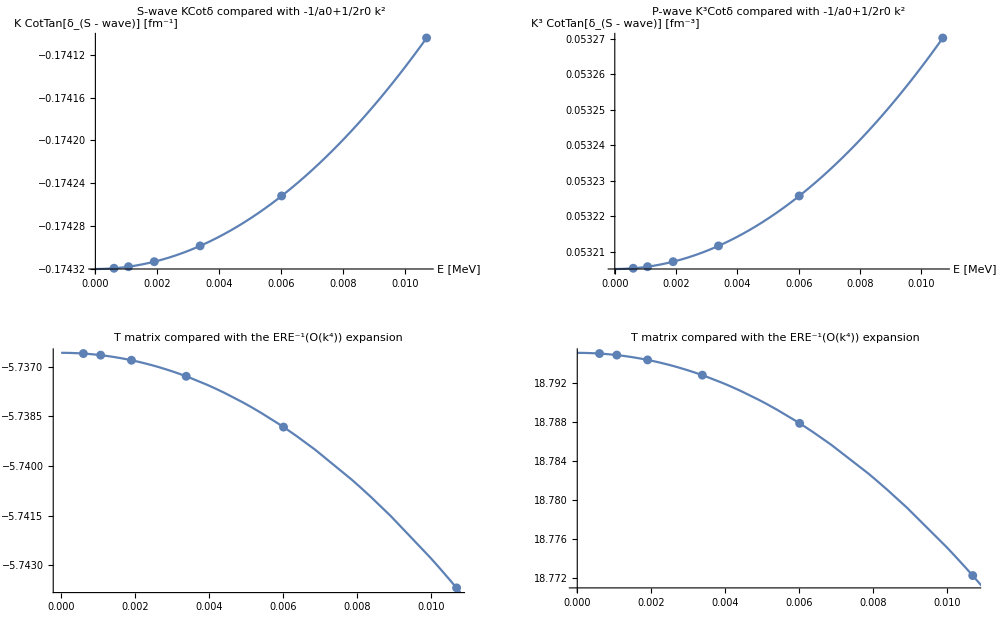

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 5.73658     r0 = 3.76617     a1 = -18.7952     r1 = 1.13723

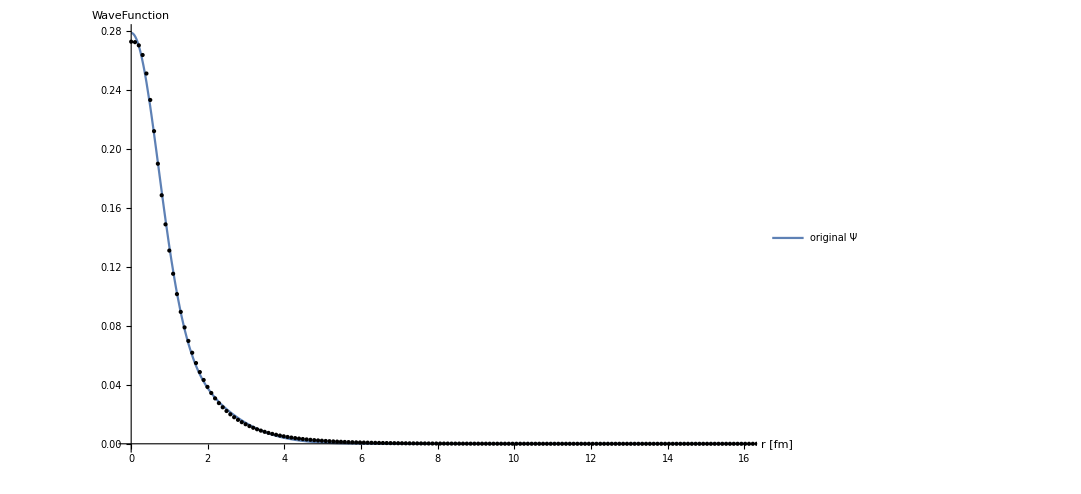

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{0.619872,1.49207},{-0.153515,0.221642},{-0.362051,1.49207},{-0.104468,0.221642},{0.346085,0.221642}}

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

S Pole Poitions in momentum: {-0.54834-0.549691 ⅈ,-0.439991+0.549691 ⅈ,0.439991+0.549691 ⅈ,0.54834-0.549691 ⅈ}

S Pole Poitions in energy:   {-0.0410358+16.6668 ⅈ,-3.00162-13.3735 ⅈ,-3.00162+13.3735 ⅈ,-0.0410358-16.6668 ⅈ}

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

P Pole Poitions in momentum: {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

P Pole Poitions in energy:   {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

-2.53859-0.934817 p^2-8.49428 p^4

Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,ComplexInfinity},{0.003382,89.1663},{0.00601414,89.0947},{0.0106948,88.8704}},{1,p^2,p^4},p]

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ListPlot::prng: Value of option PlotRange -> {{0.000601414,ComplexInfinity},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

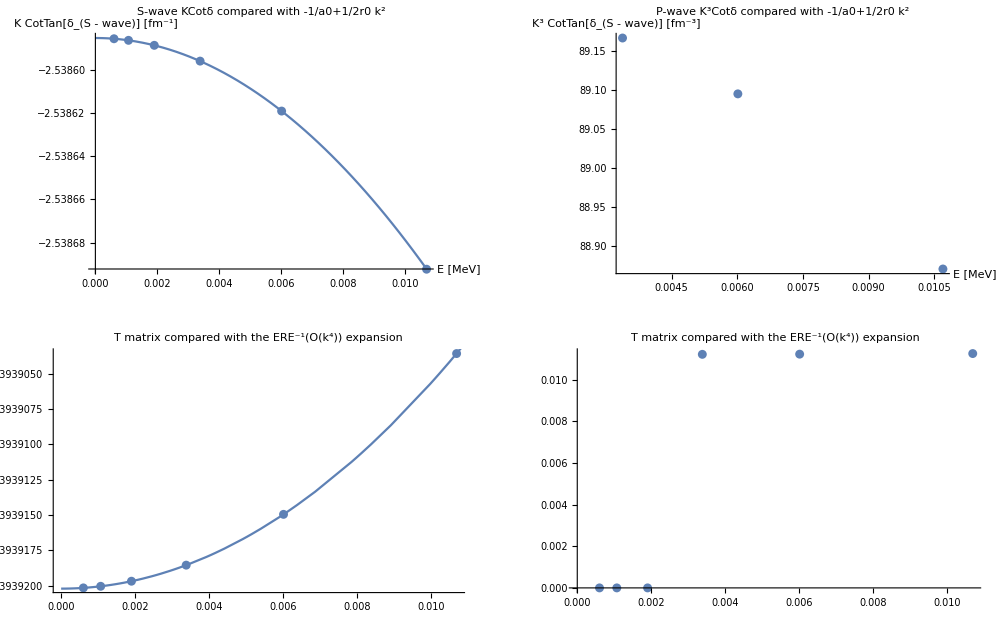

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 0.39392     r0 = -1.86984     a1 = -1/Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,ComplexInfinity},{0.003382,89.1663}},{1,p^2},p]     r1 = 0.

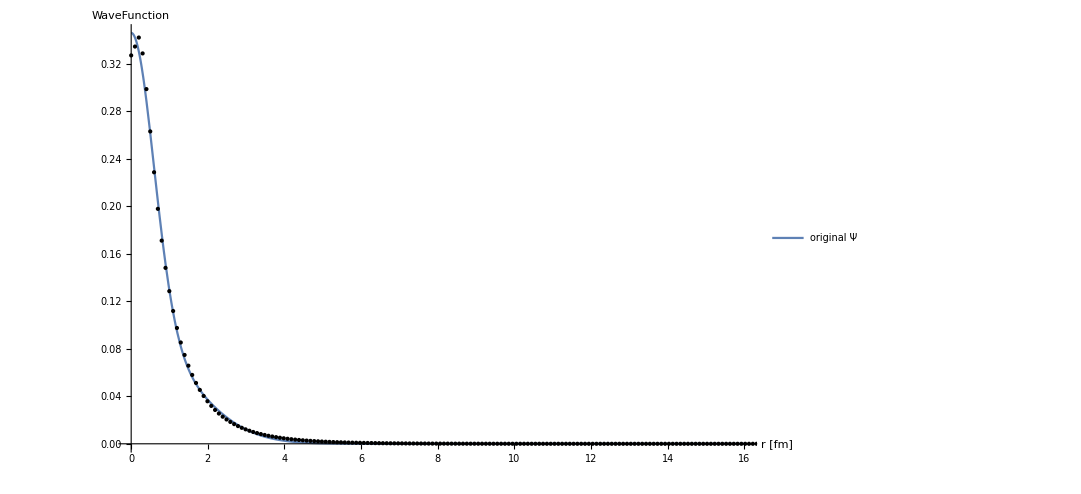

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{0.215526,0.162912},{-0.487277,0.873235},{0.699539,0.87324},{-0.152304,0.162912},{-0.0230075,0.87306}}

S Pole Poitions in momentum: {-0.257532+0.285165 ⅈ,0.+0.343897 ⅈ,0.-0.914228 ⅈ,0.257532+0.285165 ⅈ}

S Pole Poitions in energy:   {-0.414613-4.0608 ⅈ,-3.26972+0. ⅈ,-23.108+0. ⅈ,-0.414613+4.0608 ⅈ}

P Pole Poitions in momentum: {-0.180739-0.48274 ⅈ,0.+0.265503 ⅈ,0.-7.5314 ⅈ,0.180739-0.48274 ⅈ}

P Pole Poitions in energy:   {-5.53974+4.82445 ⅈ,-1.94891+0. ⅈ,-1568.21+0. ⅈ,-5.53974-4.82445 ⅈ}

-0.176151+1.86719 p^2+3.79482 p^4

0.0645462+0.641591 p^2-0.121486 p^4

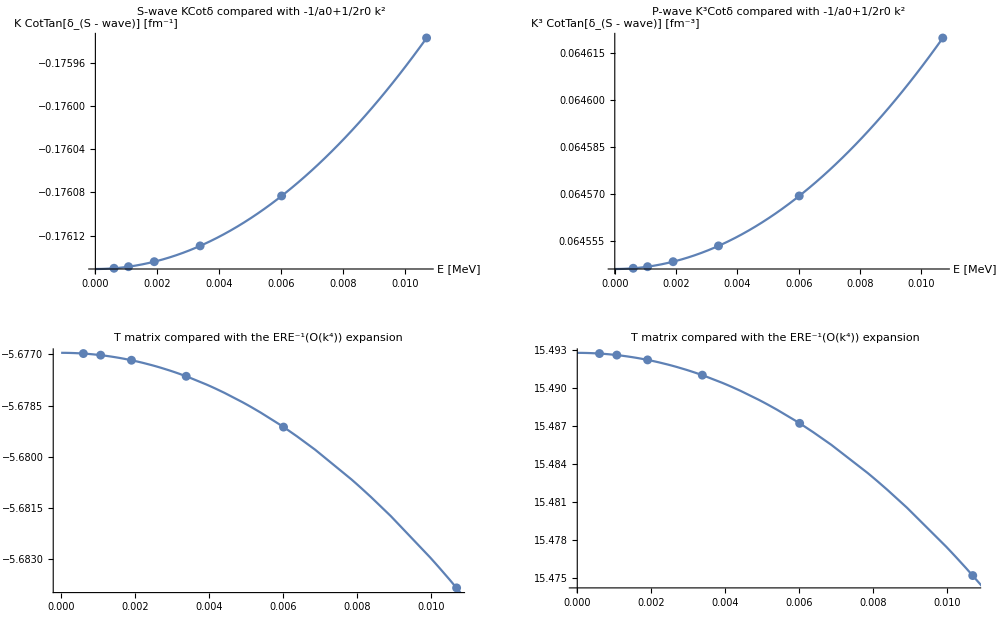

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 5.67696     r0 = 3.73447     a1 = -15.4928     r1 = 1.28318

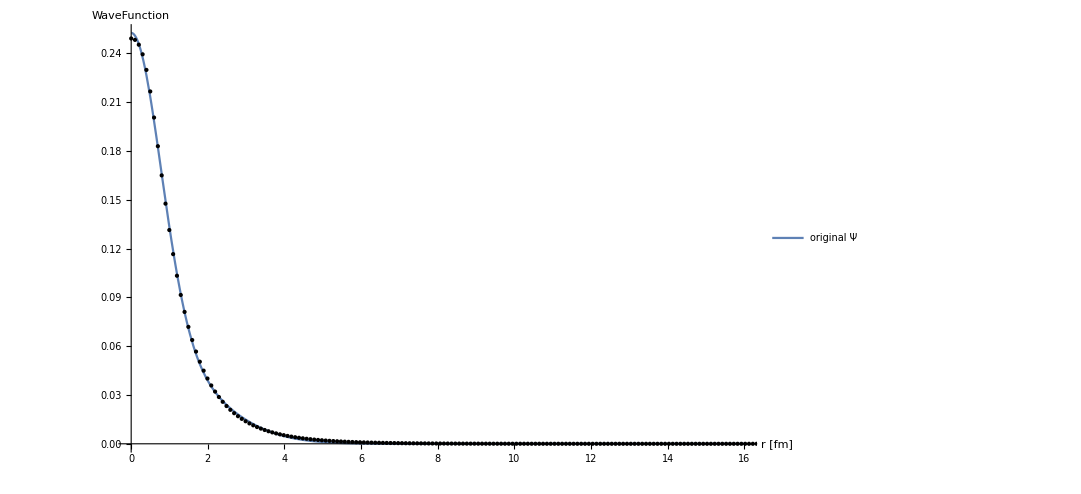

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{0.662887,0.178361},{0.208733,1.03021},{-0.24692,0.178323},{-0.0591021,0.178304},{-0.286906,0.178354}}

S Pole Poitions in momentum: {-0.224761+0.243814 ⅈ,0.+0.29876 ⅈ,0.-0.786389 ⅈ,0.224761+0.243814 ⅈ}

S Pole Poitions in energy:   {-0.24684-3.03014 ⅈ,-2.46774+0. ⅈ,-17.0973+0. ⅈ,-0.24684+3.03014 ⅈ}

P Pole Poitions in momentum: {-0.281487-0.500434 ⅈ,0.+0.207188 ⅈ,0.-0.558485 ⅈ,0.281487-0.500434 ⅈ}

P Pole Poitions in energy:   {-4.73321+7.78912 ⅈ,-1.18681+0. ⅈ,-8.62335+0. ⅈ,-4.73321-7.78912 ⅈ}

-0.153609+2.15691 p^2+5.94582 p^4

0.0282114+0.418262 p^2-0.739555 p^4

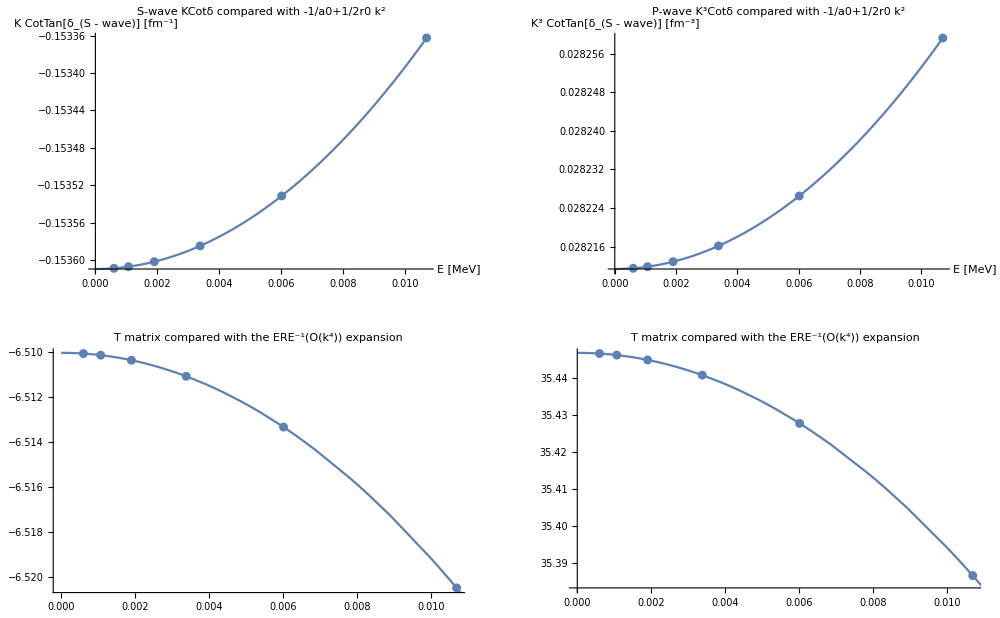

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 6.51002     r0 = 4.31397     a1 = -35.4467     r1 = 0.836507

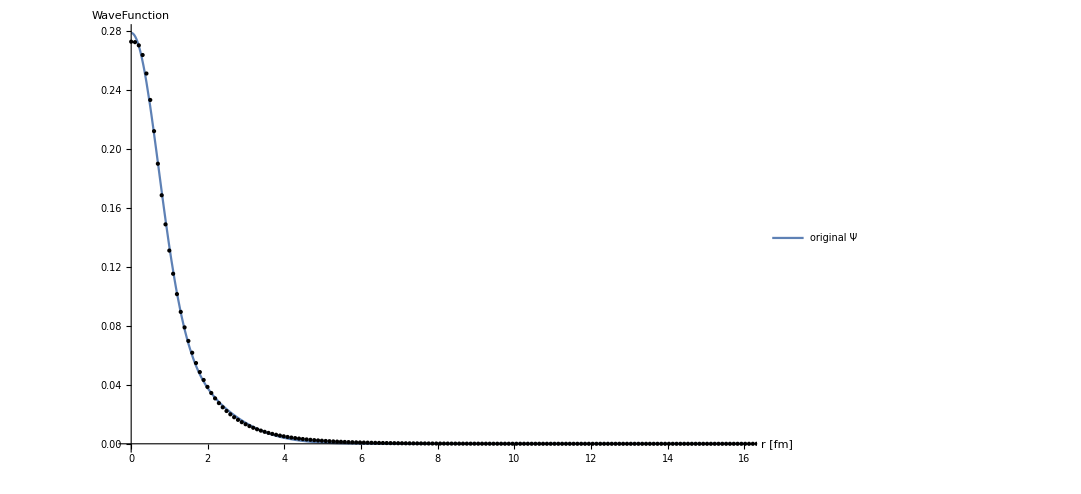

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-0.367364,0.231355},{0.182867,0.104991},{0.238403,1.60986},{-0.14987,0.105001},{0.44261,0.254922}}

S Pole Poitions in momentum: {-0.308915+0.344882 ⅈ,0.+0.415451 ⅈ,0.-1.10522 ⅈ,0.308915+0.344882 ⅈ}

S Pole Poitions in energy:   {-0.650139-5.89105 ⅈ,-4.77192+0. ⅈ,-33.7713+0. ⅈ,-0.650139+5.89105 ⅈ}

P Pole Poitions in momentum: {-0.218042-0.500963 ⅈ,0.+0.330966 ⅈ,0.+2.98502 ⅈ,0.218042-0.500963 ⅈ}

P Pole Poitions in energy:   {-5.62408+6.03989 ⅈ,-3.02845+0. ⅈ,-246.347+0. ⅈ,-5.62408-6.03989 ⅈ}

-0.211872+1.551 p^2+2.15248 p^4

0.127441+0.879808 p^2+0.432141 p^4

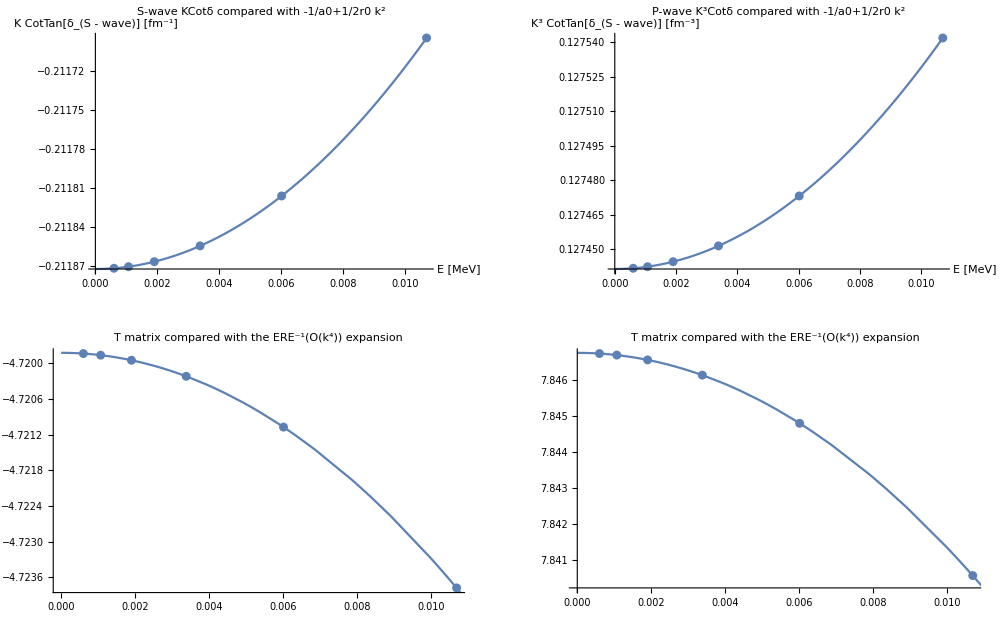

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 25.0000 ; R_max = 11.2000:   a0 = 4.71982     r0 = 3.10206     a1 = -7.84675     r1 = 1.75963

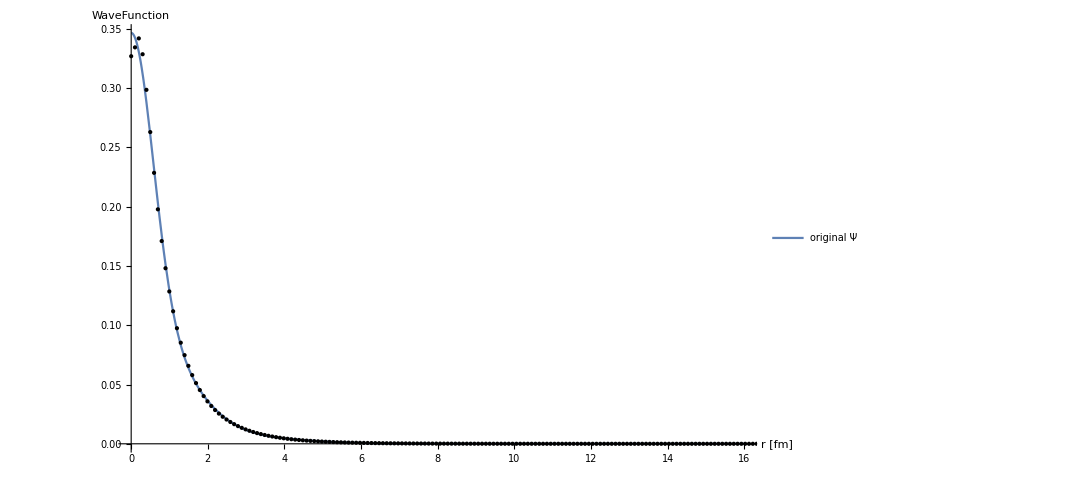

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{-0.0958377,0.0875371},{-0.0200193,0.0665304},{0.0779695,0.219609},{0.117116,0.0786968},{0.173655,0.936033}}

S Pole Poitions in momentum: {-0.192685+0.213579 ⅈ,0.+0.259682 ⅈ,0.-0.686841 ⅈ,0.192685+0.213579 ⅈ}

S Pole Poitions in energy:   {-0.234685-2.27557 ⅈ,-1.86439+0. ⅈ,-13.0426+0. ⅈ,-0.234685+2.27557 ⅈ}

P Pole Poitions in momentum: {-0.128419-0.333268 ⅈ,0.+0.182739 ⅈ,0.-4.04925 ⅈ,0.128419-0.333268 ⅈ}

P Pole Poitions in energy:   {-2.61479+2.36649 ⅈ,-0.923247+0. ⅈ,-453.318+0. ⅈ,-2.61479-2.36649 ⅈ}

-0.132322+2.49327 p^2+8.96597 p^4

0.0208223+0.433433 p^2-0.220602 p^4

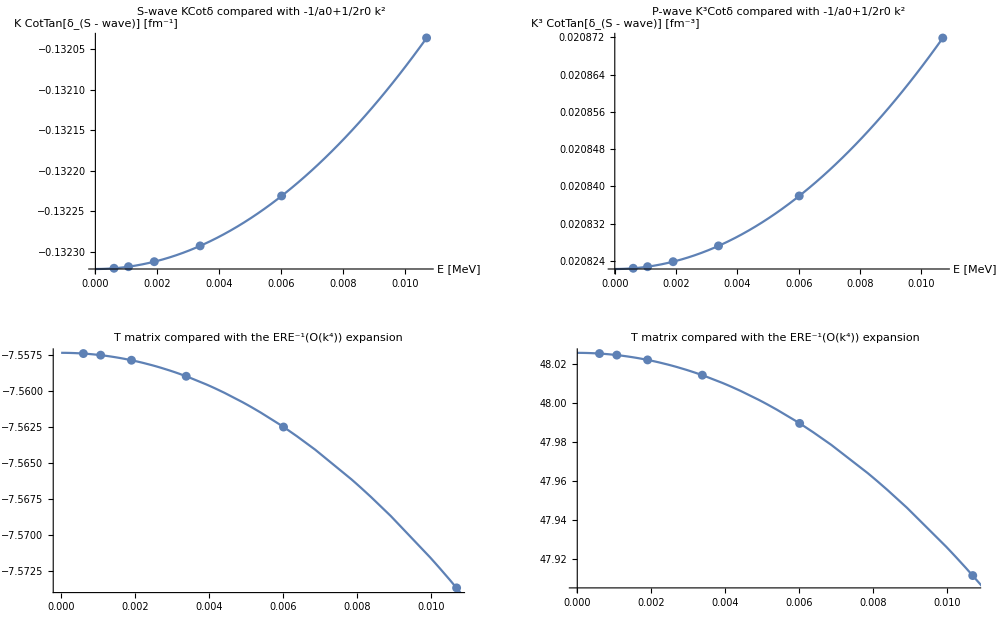

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 2.2500 ; R_max = 11.2000:   a0 = 7.55735     r0 = 4.98675     a1 = -48.0255     r1 = 0.866861

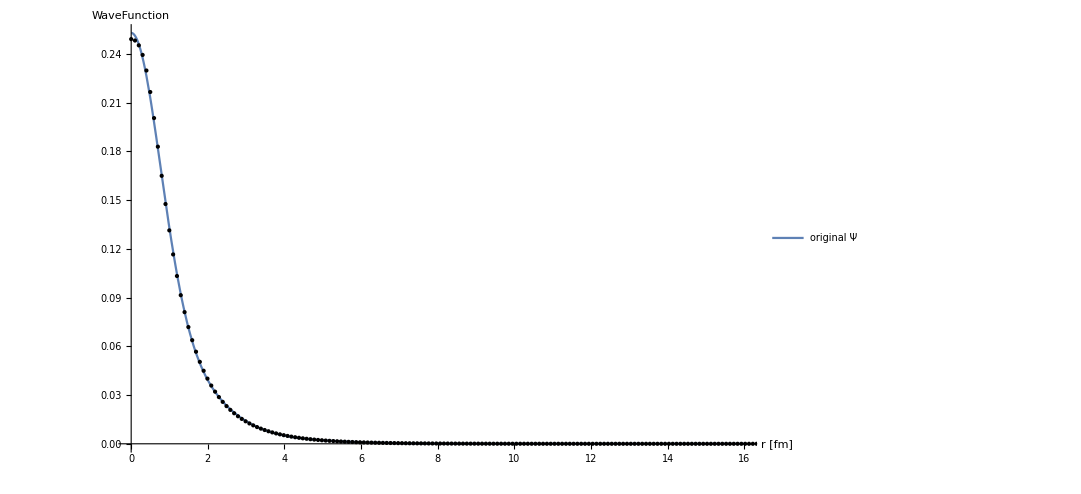

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{0.121498,0.705095},{-0.0314292,10.2276},{0.0574113,0.229482},{0.0103939,0.0684177},{0.114824,2.04758}}

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

S Pole Poitions in momentum: {-0.39112-0.482594 ⅈ,-0.349541+0.482594 ⅈ,0.349541+0.482594 ⅈ,0.39112-0.482594 ⅈ}

S Pole Poitions in energy:   {-2.20963+10.437 ⅈ,-3.06106-9.32745 ⅈ,-3.06106+9.32745 ⅈ,-2.20963-10.437 ⅈ}

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

P Pole Poitions in momentum: {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

P Pole Poitions in energy:   {Indeterminate,Indeterminate,Indeterminate,Indeterminate}

-4.60952-6.41367 p^2-33.6428 p^4

Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,58.9847},{0.003382,58.9751},{0.00601414,58.9448},{0.0106948,58.8498}},{1,p^2,p^4},p]

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ListPlot::prng: Value of option PlotRange -> {{0.000601414,ComplexInfinity},All} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

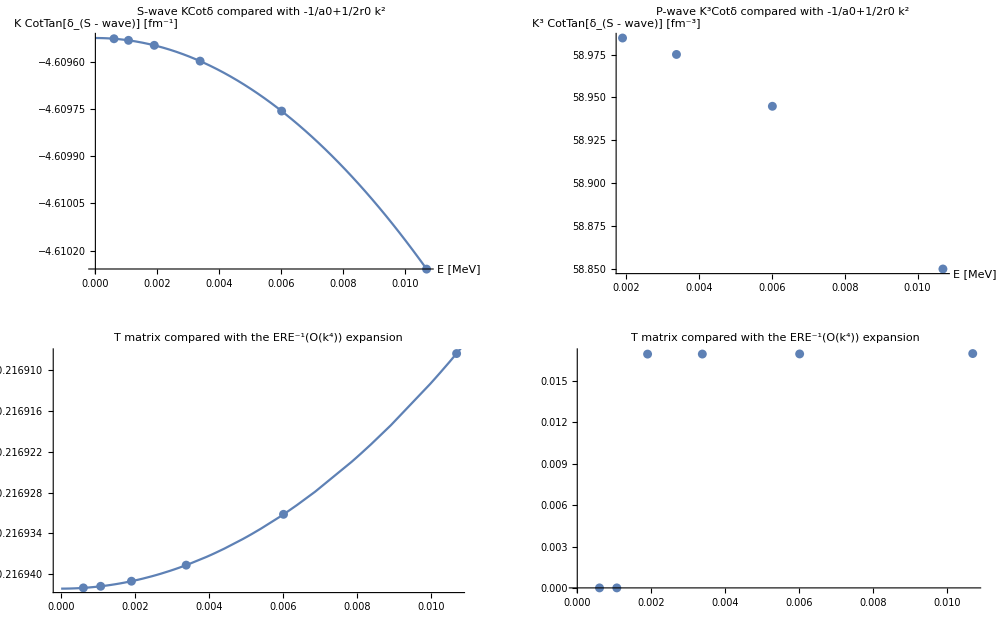

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

λ = Λ^2/4 = 4.0000 ; R_max = 11.2000:   a0 = 0.216942     r0 = -12.8282     a1 = -1/Fit[{{0.000601414,ComplexInfinity},{0.00106948,ComplexInfinity},{0.00190184,58.9847},{0.003382,58.9751}},{1,p^2},p]     r1 = 0.

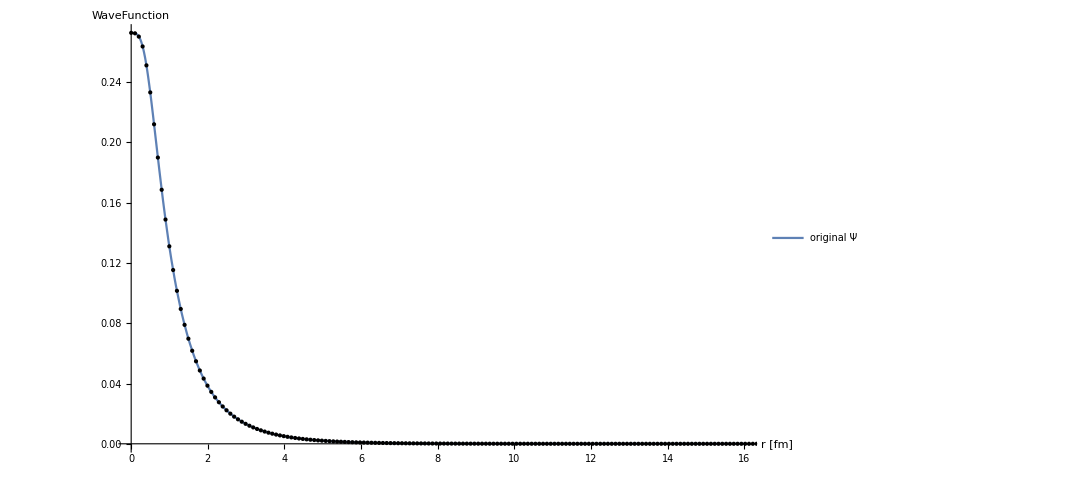

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495  core={{-0.605075,0.10538},{0.238396,1.60988},{0.638009,0.105353},{0.40551,0.256112},{-0.330194,0.230174}}

```mathematica
rGrid={11.2}; (* Subdivide[6.5,12.1,1] *)
rr=rGrid[[1]];
nk=5;
lRange={3,4,7};
nCycl=10;
rmip=0.0;
rmap=21;
EREs={};
exportdata={};

nGrid=60;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.001;
k0FMax=0.007;
Divisions=6;
rmip=0.0;
rmap=16;
Do[

wfCores={};
wfs={};
w1=1;
cmin=-0.5;cmax=1;
amin=0.01;amax=0.25;
w2=-1;
Do[
data=MϕNfit[[ll]][[w1;;w2]];

modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{cmin,cmax}]},{bLn@i,RandomReal[{amin,amax}]}},{i,nk}],1],rrel];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];
,{ll,Range[Length[wflambdas]]}];

(*---------------------*)
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
Erange1onfm=Sqrt[mh2 ErangeMeV];

Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[ll]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;

mycore=wfCores[[ll]];

Print["nn=",nn,"  nwf=",ll,"  λ=",λ,"  C0=",C0,"  D0=",D0,"  core=",mycore];
ERE=GetERE[mycore,λ];
PlotERE;
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧];
tmpwfs=Total[#⟦1⟧ⅇ^(-#⟦2⟧ r^2)&/@mycore];
Plot[tmpwfs,{r,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->400]//Print;
AppendTo[exportdata,Join[{λ,nGrid,rr},ERE[[;;4]],Flatten[mycore](*,Polesp,PolesE,Polepp,PolepE*)]];
,{ll,lRange}];
,{rr,rGrid}];

,{ncycle,Range[nCycl]}]
Export["/tmp/tmp.dat",exportdata,"Table"];
```

```mathematica
model=a+b/x+c/x^2;
l0=2;
lambdas=exportdata[[All,1]];
a0s=Transpose[{lambdas,exportdata[[All,4]]}];
fita0=model/.FindFit[a0s[[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,exportdata[[All,5]]}];
fitr0=model/.FindFit[r0s[[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,exportdata[[All,6]]}];
fita1=model/.FindFit[a1s[[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,exportdata[[All,7]]}];
fitr1=model/.FindFit[r1s[[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[rr];
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,lambdas[[-1]]},ImageSize->Large]]
}}]
```

-Graphics-

```mathematica
ComplexPlot
```

```mathematica
cplxpoleSp=Transpose[{Re[exportdata[[All,8+#]]],Im[exportdata[[All,8+#]]]}]&/@{0,1,2,3};
cplxpolePp=Transpose[{Re[exportdata[[All,16+#]]],Im[exportdata[[All,16+#]]]}]&/@{0,1,2,3};
GraphicsGrid[{{
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpoleSp]
,
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpolePp]
}}
]
```

-Graphics-

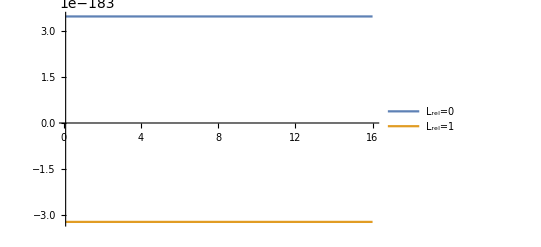

-Graphics3D-

9.

-1090.55

6552.5

```mathematica
nwf=5;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rprime=2.1;sca=1.;rMax=16;
Plot[{WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],0,mh2],WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},PlotRange->Full,PlotLegends->{"L_rel=0","L_rel=1"}]

Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[ErangeMeV[[1]]],"E="<>ToString[ErangeMeV[[2]]]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->750]
λ
C0
D0
```